## Level-set 3D

#### utility

```mathematica
SetSystemOptions["SparseArrayOptions"->{"TreatRepeatedEntries"->1}]; (*Thank you, Oliver!*)
```

```mathematica
infoData[data_]:=ListAnimate[Table[
TableForm[{
{ListLinePlot[{data[[2]]},PlotTheme->"Detailed",ImageSize->Medium,Epilog->{Red,DotDashed,AbsoluteThickness[2],InfiniteLine[{{xMove,0},{xMove,1}}]},PlotLabel->"Objective Function Value"],ListLinePlot[{data[[3]]},PlotTheme->"Detailed",ImageSize->Medium,PlotRange->All,Epilog->{Red,DotDashed,AbsoluteThickness[2],InfiniteLine[{{xMove,0},{xMove,1}}]},PlotLabel->"Current Volume"],
ListLinePlot[{data[[6]]},PlotTheme->"Detailed",PlotRange->All,ImageSize->Medium,Epilog->{Red,DotDashed,AbsoluteThickness[2],InfiniteLine[{{xMove,0},{xMove,1}}]},PlotLabel->"ObjValue Variance"]},
{ListLinePlot[{data[[4]]},PlotTheme->"Detailed",ImageSize->Medium,PlotRange->All,Epilog->{Red,DotDashed,AbsoluteThickness[2],InfiniteLine[{{xMove,0},{xMove,1}}]},PlotLabel->"First Legrange Value"],ListLinePlot[{data[[5]]},PlotTheme->"Detailed",ImageSize->Medium,Epilog->{Red,DotDashed,AbsoluteThickness[2],InfiniteLine[{{xMove,0},{xMove,1}}]},PlotLabel->"Second Legrange Value"],
TableForm[data[[7]]]}}],
{xMove,0,Length[data[[2]]],1}]];
```

#### stiffnessMatrix

```mathematica
keM[ν_]:=Block[
{KE,k,k1,k2,k3,k4,k5,k6},
k=1/144(*72*)*Transpose[{{32,6,-8,6,-6,4,3,-6,-10,3,-3,-3,-4,-8},{-48,0,0,-24,24,0,0,0,12,-12,0,12,12,12}}].{1,ν};

k1=
{
{k[[1]],k[[2]],k[[2]],k[[3]],k[[5]],k[[5]]},
{k[[2]],k[[1]],k[[2]],k[[4]],k[[6]],k[[7]]},
{k[[2]],k[[2]],k[[1]],k[[4]],k[[7]],k[[6]]},
{k[[3]],k[[4]],k[[4]],k[[1]],k[[8]],k[[8]]},
{k[[5]],k[[6]],k[[7]],k[[8]],k[[1]],k[[2]]},
{k[[5]],k[[7]],k[[6]],k[[8]],k[[2]],k[[1]]}
};

k2=
{
{k[[9]],k[[8]],k[[12]],k[[6]],k[[4]],k[[7]]},
{k[[8]],k[[9]],k[[12]],k[[5]],k[[3]],k[[5]]},
{k[[10]],k[[10]],k[[13]],k[[7]],k[[4]],k[[6]]},
{k[[6]],k[[5]],k[[11]],k[[9]],k[[2]],k[[10]]},
{k[[4]],k[[3]],k[[5]],k[[2]],k[[9]],k[[12]]},
{k[[11]],k[[4]],k[[6]],k[[12]],k[[10]],k[[13]]}
};

k3=
{
{k[[6]],k[[7]],k[[4]],k[[9]],k[[12]],k[[8]]},
{k[[7]],k[[6]],k[[4]],k[[10]],k[[13]],k[[10]]},
{k[[5]],k[[5]],k[[3]],k[[8]],k[[12]],k[[9]]},
{k[[9]],k[[10]],k[[2]],k[[6]],k[[11]],k[[5]]},
{k[[12]],k[[13]],k[[10]],k[[11]],k[[6]],k[[4]]},
{k[[2]],k[[12]],k[[9]],k[[4]],k[[5]],k[[3]]}
};

k4=
{
{k[[14]],k[[11]],k[[11]],k[[13]],k[[10]],k[[10]]},
{k[[11]],k[[14]],k[[11]],k[[12]],k[[9]],k[[8]]},
{k[[11]],k[[11]],k[[14]],k[[12]],k[[8]],k[[9]]},
{k[[13]],k[[12]],k[[12]],k[[14]],k[[7]],k[[7]]},
{k[[10]],k[[9]],k[[8]],k[[7]],k[[14]],k[[11]]},
{k[[10]],k[[8]],k[[9]],k[[7]],k[[11]],k[[14]]}
};

k5=
{
{k[[1]],k[[2]],k[[8]],k[[3]],k[[5]],k[[4]]},
{k[[2]],k[[1]],k[[8]],k[[4]],k[[6]],k[[11]]},
{k[[8]],k[[8]],k[[1]],k[[5]],k[[11]],k[[6]]},
{k[[3]],k[[4]],k[[5]],k[[1]],k[[8]],k[[2]]},
{k[[5]],k[[6]],k[[11]],k[[8]],k[[1]],k[[8]]},
{k[[4]],k[[11]],k[[6]],k[[2]],k[[8]],k[[1]]}
};

k6=
{
{k[[14]],k[[11]],k[[7]],k[[13]],k[[10]],k[[12]]},
{k[[11]],k[[14]],k[[7]],k[[12]],k[[9]],k[[2]]},
{k[[7]],k[[7]],k[[14]],k[[10]],k[[2]],k[[9]]},
{k[[13]],k[[12]],k[[10]],k[[14]],k[[7]],k[[11]]},
{k[[10]],k[[9]],k[[2]],k[[7]],k[[14]],k[[7]]},
{k[[12]],k[[2]],k[[9]],k[[11]],k[[7]],k[[14]]}
};

KE=ArrayFlatten[1/((ν+1)*(1-2*ν))*{{k1,k2,k3,k4},{Transpose[k2],k5,k6,Transpose[k3]},{Transpose[k3],k6,Transpose[k5],Transpose[k2]},{k4,k3,k2,Transpose[k1]}}];
KE
]
```

#### bwdist3D

```mathematica
bwdist3D[Array_]:=ImageData[DistanceTransform[Image3D[Map[If[#==0,1,0]&,Array,{3}]], DistanceFunction->EuclideanDistance]]
```

#### reinit3D

```mathematica
reinit3D[struc_]:=Block[
{str=struc,strucFull},
strucFull=ArrayPad[str,1];
Map[If[#==0,1,0]&,strucFull,{3}]*(bwdist3D[strucFull]-0.5)-strucFull*(bwdist3D[strucFull-1]-0.5)
]
```

#### evolve3D

```mathematica
evolve3D[v_,g_,lsf_,stepLength_,w_,timeStep_]:=Block[
{vFull,gFull,dt,i,lsfup=lsf,dpx,dmx,dpy,dmy,dpz,dmz,strucFull,strucup},

vFull=ArrayPad[v,1];
gFull=ArrayPad[g,1];

(*Print[{"test",MatrixForm@(v)}];*)

dt=0.1/(Max[Abs[Flatten[v]]]*timeStep);

For[i=1,i≤(stepLength*10*timeStep),i++,

dpx=RotateRight[lsfup,{0,-1,0}]-lsfup;
dmx=lsfup-RotateRight[lsfup,{0,1,0}];
dpy=RotateRight[lsfup,{-1,0,0}]-lsfup;
dmy=lsfup-RotateRight[lsfup,{1,0,0}];
dpz=RotateRight[lsfup,{0,0,-1}]-lsfup;
dmz=lsfup-RotateRight[lsfup,{0,0,1}];

lsfup=lsfup-dt*Map[Min[#,0]&,vFull,{3}]*Sqrt[Map[Min[#,0]&,dmx,{3}]^2+Map[Max[#,0]&,dpx,{3}]^2+Map[Min[#,0]&,dmy,{3}]^2+Map[Max[#,0]&,dpy,{3}]^2+Map[Min[#,0]&,dmz,{3}]^2+Map[Max[#,0]&,dpz,{3}]^2]-dt*Map[Max[#,0]&,vFull,{3}]*Sqrt[Map[Max[#,0]&,dmx,{3}]^2+Map[Min[#,0]&,dpx,{3}]^2+Map[Max[#,0]&,dmy,{3}]^2+Map[Min[#,0]&,dpy,{3}]^2+Map[Max[#,0]&,dmz,{3}]^2+Map[Min[#,0]&,dpz,{3}]^2]-w*dt*gFull;

];

strucFull=Map[Boole[#<0]&,lsfup,{3}];
strucup=strucFull[[2;;-2,2;;-2,2;;-2]];
{strucup,lsfup}
]
```

#### updateStep3D

```mathematica
Image3D[{{{0,1,0},{1,2,1},{0,1,0}},{{1,2,1},{2,3,2},{1,2,1}},{{0,1,0},{1,2,1},{0,1,0}}}]
```

-Graphics3D-

```mathematica
updateStep3D[lsF_,shapeS_,topS_,stepLength_,topWeight_,timeStep_]:=Block[
{shapeSens=shapeS,topSens=topS,lsf=lsF,l1,l2,l3,l4,l5,l6,struc,kernel1,kernel2},
kernel1={{{0,1,0},{1,2,1},{0,1,0}},{{1,2,1},{2,3,2},{1,2,1}},{{0,1,0},{1,2,1},{0,1,0}}};
kernel2={{{0,0,0},{0,1,0},{0,0,0}},{{0,1,0},{1,2,1},{0,1,0}},{{0,0,0},{0,1,0},{0,0,0}}};
shapeSens=ListConvolve[1/(Total[Flatten[kernel2]])*kernel2,ArrayPad[shapeSens,{1,1},"Fixed"]];
(*topSens=ListConvolve[1/6*{{{0,1,0},{1,2,1},{0,1,0}},{{1,2,1},{2,3,2},{1,2,1}},{{0,1,0},{1,2,1},{0,1,0}}},ArrayPad[topSens,{1,1},"Fixed"]];*)
(*{{{0,0,0},{0,1,0},{0,0,0}},{{0,1,0},{1,2,1},{0,1,0}},{{0,0,0},{0,1,0},{0,0,0}}}*)
(*Чувствительность вблизи зоны закрепления и приложения сил зануляем, вернуть при неправильной работе, сейчас вставлена*)
{l1,l2,l3}=Dimensions[shapeSens];
(*nely,nelx,nelz*)
(*shapeSens[[1,1,1]]=shapeSens[[l1,1,1]]=shapeSens[[l1,1,l3]]=shapeSens[[1,1,l3]]=shapeSens[[l1/2,l2,l3]]=shapeSens[[l1/2+1,l2,l3]]=0;*)
(*topSens[[1,1,1]]=topSens[[l1,1,1]]=topSens[[l1,1,l3]]=topSens[[1,1,l3]]=topSens[[l1/2,l2,l3]]=topSens[[l1/2+1,l2,l3]]=0;*)

{struc,lsf}=evolve3D[-shapeSens,topSens*Map[If[#<0,1,0]&,lsf[[2;;-2,2;;-2,2;;-2]],{3}],lsf,stepLength,topWeight,timeStep]
]
```

#### toplevelset3D

```mathematica
toplevelset3D[nelX_,nelY_,nelZ_,volReQ_,stepLengtH_,numReiniT_,topWeighT_,maxIter_,α_,lainit_,Lainit_,timeStep_]:=Block[{nelx=nelX,nely=nelY,nelz=nelZ,volReq=volReQ,stepLength=stepLengtH,numReinit=numReiniT,topWeight=topWeighT,pr,ym,λ,μ,il,jl,kl,loadnid,loaddof,pts,nid,fixednid,fixeddof,struc,shapeSens,topSens,volCurr,lsf,nele,ndof,f,freedofs,testKE,nodegrd,nodeids,nodeidz,edofMat,edofVec,edof,iK,jK,sK,k,iterNum,K,elz,ely,elx,La,la,alpha=α,ue,ce,u,constL,objData,volData,laData,LaData,varianceData,expdata,jf,kf,koef,i,j,strucData},

objData={};
volData={};
laData={};
LaData={};
varianceData={};
strucData={};
expdata={{"nelx",nelx},{"nely",nely},{"nelz",nelz},{"α",alpha},{"λ1",lainit},{"λ2",Lainit},{"volReq",volReq}};

pr=0.3;
ym=1;
koef=1;

λ=ym*pr/((1+pr)*(1-pr));
μ=ym/2/(1+pr);
	
     struc=ConstantArray[1.,{nely,nelx,nelz}];
For[i=1,i≤nely-1,i++,For[j=1,j≤nelx-1,j++,For[k=1,k≤nelz-1,k++,If[Divisible[i,3]&&Divisible[j,7]&&Divisible[k,3],struc[[i,j,k]]=0;]]]];
shapeSens=ConstantArray[0.,{nely,nelx,nelz}];
topSens=ConstantArray[0.,{nely,nelx}];
volCurr=Total[Flatten[struc]]/nelx/nely/nelz;
lsf=reinit3D[struc];

il=nelx;
jl=0;
kl={nelz/2}(*Range[0,nelz]*);
pts={{nelx,nely/2,nelz/2},{nelx,nely/2+1,nelz/2},{nelx,nely/2,nelz/2+1},{nelx,nely/2+1,nelz/2+1}};
nid=Apply[#3*(nelx+1)*(nely+1)+#1*(nely+1)+(nely+1-#2)&]/@pts;
loadnid=nid;
loaddof=3*Flatten[loadnid]-1;

pts={{0,0,0},{0,0,nelz},{0,nely,nelz},{0,nely,0}};
nid=Apply[#3*(nelx+1)*(nely+1)+#1*(nely+1)+(nely+1-#2)&]/@pts;

{jf,kf}={Array[#2&,{nelz+1,nely+1}],Array[#1&,{nelz+1,nely+1}]};
fixednid=nid(*(kf-1)*(nely+1)*(nelx+1)+jf*);
fixeddof={3*Flatten[Transpose[{fixednid}]],3*Flatten[Transpose[{fixednid}]]-1,3*Flatten[Transpose[{fixednid}]]-2};

nele=nelx*nely*nelz;
ndof=3*(nelx+1)*(nely+1)*(nelz+1);
f=SparseArray[Thread[loaddof->-1],ndof];
u=ConstantArray[0,ndof];
freedofs=Complement[Range[1,ndof],Flatten[fixeddof]];
testKE=keM[pr];
nodegrd=Transpose[ArrayReshape[Range[1,(nely+1)*(nelx+1)],{nelx+1,nely+1}]];
nodeids=ArrayReshape[Transpose[nodegrd[[1;;-2,1;;-2]]],{nelx*nely,1}];
nodeidz=Range[0,(nelz-1)*(nely+1)*(nelx+1),(nelx+1)*(nely+1)];nodeids=Flatten[Transpose@Table[nodeids,Length[nodeidz]],{3}][[1]]+Table[nodeidz,Length[nodeids]];
edofVec=3*Flatten[Transpose@nodeids]+1;
edofMat=Transpose[Table[edofVec,24]]+ArrayFlatten[Table[Flatten[{0,1,2,3*nely+{3,4,5,0,1,2},-3,-2,-1,3*(nely+1)*(nelx+1)+{0,1,2,3*nely+{3,4,5,0,1,2},-3,-2,-1}}],nele]];iK=Transpose[ArrayReshape[KroneckerProduct[edofMat,ConstantArray[{1},24]],{24*24*nele,1}]][[1]];
jK=Transpose[ArrayReshape[KroneckerProduct[edofMat,ConstantArray[1,24]],{24*24*nele,1}]][[1]];
iterNum=1;

While[iterNum ≤maxIter(*&&volCurr>volReq*0.99*),

sK=ArrayReshape[Transpose[(Transpose[{Flatten[testKE]}].{Map[If[#<1,0.001,1]&,Flatten[struc]]})],{24*24*nele,1}];
K=SparseArray[(Transpose[{iK,jK}])->Flatten[Transpose[sK]]];K=(K+Transpose[K])/2;

u[[freedofs]]=LinearSolve[K[[freedofs,freedofs]],f[[freedofs]]];
ce=ArrayReshape[Total[#]&/@((u[[#]]&/@edofMat).testKE*(u[[#]]&/@edofMat)),{nely,nelx,nelz}];

shapeSens=-Map[Max[#,0.001]&,struc,{3}]*ce;


(*V.J.Challis Legrange parameters*)
If[
iterNum==1
,
la=lainit;
La=Lainit;
,
la=la-1/La*(volCurr-volReq);
La=alpha*La;
];

If[
iterNum≥12,
If[
volData[[iterNum-1]]-volData[[iterNum-6]]==0,
koef=koef*1.1;
]
];

la=-Max[Abs[shapeSens-Max[shapeSens]]]*0.1*koef;

AppendTo[objData,Total[Flatten@shapeSens]];
AppendTo[volData,volCurr];
AppendTo[laData,la];
AppendTo[LaData,La];
AppendTo[strucData,struc];
AppendTo[varianceData,Variance[Flatten[shapeSens]]];
If[
Divisible[iterNum,4]
,
(*Print["=========================================="];*)
Print[StringJoin[ToString[iterNum]," iterations done"]];
Print[Image3D[struc]];
Print[StringJoin[ToString[volCurr*100]," % volume"]];(*
Print[StringJoin[ToString[la]," 1st legrange parameter"]];
Print[StringJoin[ToString[La]," 2nd legrange parameter"]];*)
Print[StringJoin[ToString[Max[Abs[shapeSens]]]," shapeSens max module"]];
(*Print[Image3D[Abs[shapeSens-Max[shapeSens]]]];*)
];

shapeSens=shapeSens-la(*+1/La*)*(volCurr-volReq);
topSens=topSens+Pi*(la-1/La*(volCurr-volReq));

If[
Divisible[iterNum,4]
,
(*Print["=========================================="];*)
(*Print[StringJoin[ToString[iterNum]," iterations done"]];
Print[Image3D[struc]];*)
(*Print[StringJoin[ToString[volCurr*100]," % volume"]];
Print[StringJoin[ToString[la]," 1st legrange parameter"]];
Print[StringJoin[ToString[La]," 2nd legrange parameter"]];*)
Print[StringJoin[ToString[Max[Abs[shapeSens]]]," shapeSens max module"]];
(*Print[Image3D[Abs[shapeSens-Max[shapeSens]]]];*)
];

(*A.A.Krotkikh parameters*)

(*constL=1;
shapeSens=shapeSens+(volCurr-volReq)*constL*Max[Abs[shapeSens]];*)

{struc,lsf}=updateStep3D[lsf,shapeSens,topSens,stepLength,topWeight,timeStep];

volCurr=N[Total[Flatten[struc]]/nelx/nely/nelz];

If[
Divisible[iterNum,numReinit]
,
lsf=reinit3D[struc];
];
iterNum=iterNum+1;

];
Print["=========================================="];
Print[StringJoin[ToString[iterNum]," iterations done"]];
Print[StringJoin[ToString[volCurr*100]," % volume"]];
Print[StringJoin[ToString[la]," 1st legrange parameter"]];
Print[StringJoin[ToString[La]," 2nd legrange parameter"]];
Print[StringJoin[ToString[Max[Abs[shapeSens]]]," shapeSens max module"]];
(*Print[Image3D[Abs[shapeSens]]];*)
Print[Image3D[struc]];
Beep[];
Return[{struc,objData,volData,laData,LaData,varianceData,expdata,strucData}]

]
```

### test

```mathematica
(*toplevelset3D[nelX_,nelY_,nelZ_,volReQ_,stepLengtH_,numReiniT_,topWeighT_,maxIter_,α_,lainit_,Lainit_]*)
```

#### dt = 0.1

```mathematica
data=toplevelset3D[30,16,16,0.3,5,5,0,200,0.95,-0.01,30.];
infoData
```

4 iterations done

-Graphics3D-

8 iterations done

-Graphics3D-

==========================================

11 iterations done

20.3646 % volume

-0.124855 1st legrange parameter

18.9075 2nd legrange parameter

4.21621 shapeSens max module

-Graphics3D-

```mathematica
data=toplevelset3D[30,16,16,0.3,5,3,0,200,0.95,-0.01,30.];
infoData
```

4 iterations done

-Graphics3D-

8 iterations done

-Graphics3D-

==========================================

10 iterations done

21.237 % volume

-0.107202 1st legrange parameter

19.9026 2nd legrange parameter

4.13485 shapeSens max module

-Graphics3D-

```mathematica
data=toplevelset3D[30,16,16,0.3,3,3,0,200,0.95,-0.01,30.];
infoData
```

4 iterations done

-Graphics3D-

8 iterations done

-Graphics3D-

12 iterations done

-Graphics3D-

==========================================

12 iterations done

27.8516 % volume

-0.171184 1st legrange parameter

17.9621 2nd legrange parameter

4.57298 shapeSens max module

-Graphics3D-

#### dt = 0.001

Изменил метод Лагранжа

```mathematica
data=toplevelset3D[30,16,16,0.3,50,3,0,100,0.95,-0.01,30.];
infoData
```

4 iterations done

-Graphics3D-

8 iterations done

-Graphics3D-

12 iterations done

-Graphics3D-

16 iterations done

-Graphics3D-

20 iterations done

-Graphics3D-

24 iterations done

-Graphics3D-

28 iterations done

-Graphics3D-

32 iterations done

-Graphics3D-

36 iterations done

-Graphics3D-

40 iterations done

-Graphics3D-

44 iterations done

-Graphics3D-

48 iterations done

-Graphics3D-

52 iterations done

-Graphics3D-

56 iterations done

-Graphics3D-

60 iterations done

-Graphics3D-

64 iterations done

-Graphics3D-

68 iterations done

-Graphics3D-

72 iterations done

-Graphics3D-

76 iterations done

-Graphics3D-

80 iterations done

-Graphics3D-

84 iterations done

-Graphics3D-

88 iterations done

-Graphics3D-

92 iterations done

-Graphics3D-

96 iterations done

-Graphics3D-

100 iterations done

-Graphics3D-

==========================================

101 iterations done

32.5911 % volume

-6.40918 1st legrange parameter

0.186964 2nd legrange parameter

5.03241 shapeSens max module

-Graphics3D-

```mathematica
data=toplevelset3D[30,16,16,0.3,50,3,0,50,0.95,-0.01,1000.];
infoData
```

4 iterations done

-Graphics3D-

8 iterations done

-Graphics3D-

12 iterations done

-Graphics3D-

16 iterations done

-Graphics3D-

20 iterations done

-Graphics3D-

24 iterations done

-Graphics3D-

28 iterations done

-Graphics3D-

32 iterations done

-Graphics3D-

36 iterations done

-Graphics3D-

40 iterations done

-Graphics3D-

44 iterations done

-Graphics3D-

48 iterations done

-Graphics3D-

==========================================

51 iterations done

100. % volume

-0.160908 1st legrange parameter

80.9947 2nd legrange parameter

3.92806 shapeSens max module

-Graphics3D-

```mathematica
data=toplevelset3D[30,16,16,0.3,50,3,0,40,0.95,-0.01,30.];
infoData
```

4 iterations done

-Graphics3D-

8 iterations done

-Graphics3D-

12 iterations done

-Graphics3D-

16 iterations done

-Graphics3D-

20 iterations done

-Graphics3D-

24 iterations done

-Graphics3D-

28 iterations done

-Graphics3D-

32 iterations done

-Graphics3D-

36 iterations done

-Graphics3D-

40 iterations done

-Graphics3D-

==========================================

41 iterations done

49.5703 % volume

-1.35734 1st legrange parameter

4.05828 2nd legrange parameter

4.60109 shapeSens max module

-Graphics3D-

#### dt = 0.01

```mathematica
data=toplevelset3D[30,16,16,0.3,3,3,0,200,0.95,-0.01,30.];
infoData
```

4 iterations done

-Graphics3D-

8 iterations done

-Graphics3D-

12 iterations done

-Graphics3D-

16 iterations done

-Graphics3D-

20 iterations done

-Graphics3D-

24 iterations done

-Graphics3D-

28 iterations done

-Graphics3D-

==========================================

31 iterations done

20.1302 % volume

-0.697256 1st legrange parameter

6.77807 2nd legrange parameter

3.97676 shapeSens max module

-Graphics3D-

```mathematica
data=toplevelset3D[30,16,16,0.3,3,3,0,200,0.95,-0.01,30.];
infoData
```

4 iterations done

8 iterations done

12 iterations done

16 iterations done

20 iterations done

24 iterations done

28 iterations done

==========================================

31 iterations done

20.1302 % volume

-0.697256 1st legrange parameter

6.77807 2nd legrange parameter

3.97676 shapeSens max module

-Graphics3D-

```mathematica
data=toplevelset3D[30,16,16,0.3,2,3,0,200,0.95,-0.01,30.];
infoData
```

4 iterations done

8 iterations done

12 iterations done

16 iterations done

20 iterations done

24 iterations done

28 iterations done

32 iterations done

36 iterations done

40 iterations done

44 iterations done

48 iterations done

52 iterations done

56 iterations done

60 iterations done

64 iterations done

68 iterations done

==========================================

70 iterations done

24.8307 % volume

-4.77945 1st legrange parameter

0.916909 2nd legrange parameter

15.5912 shapeSens max module

-Graphics3D-

```mathematica
data=toplevelset3D[30,16,16,0.3,3,3,0,200,0.9,-0.01,30.];
infoData
```

4 iterations done

8 iterations done

12 iterations done

16 iterations done

20 iterations done

24 iterations done

28 iterations done

==========================================

31 iterations done

27.2005 % volume

-1.00809 1st legrange parameter

1.41304 2nd legrange parameter

4.81535 shapeSens max module

-Graphics3D-

```mathematica
data=toplevelset3D[30,16,16,0.3,3,3,0,200,0.8,-0.01,30.];
infoData
```

4 iterations done

8 iterations done

12 iterations done

16 iterations done

20 iterations done

24 iterations done

==========================================

24 iterations done

19.4271 % volume

-2.3838 1st legrange parameter

0.221361 2nd legrange parameter

12.4084 shapeSens max module

-Graphics3D-

```mathematica
data=toplevelset3D[30,16,16,0.3,3,3,0,200,0.95,-0.01,30.];
infoData
```

4 iterations done

8 iterations done

12 iterations done

16 iterations done

20 iterations done

==========================================

22 iterations done

20.0781 % volume

-0.455711 1st legrange parameter

10.7546 2nd legrange parameter

3.90456 shapeSens max module

-Graphics3D-

```mathematica
data=toplevelset3D[30,16,16,0.3,3,3,0,200,0.95,-0.01,1000.];
infoData
```

4 iterations done

8 iterations done

12 iterations done

16 iterations done

20 iterations done

24 iterations done

28 iterations done

32 iterations done

36 iterations done

40 iterations done

44 iterations done

48 iterations done

52 iterations done

56 iterations done

60 iterations done

64 iterations done

68 iterations done

72 iterations done

76 iterations done

==========================================

76 iterations done

20.8594 % volume

-0.42098 1st legrange parameter

22.4671 2nd legrange parameter

4.25458 shapeSens max module

-Graphics3D-

```mathematica
data=toplevelset3D[30,16,16,0.3,3,3,0,200,0.90,-0.01,1000.];
infoData
```

4 iterations done

8 iterations done

12 iterations done

16 iterations done

20 iterations done

24 iterations done

28 iterations done

32 iterations done

36 iterations done

40 iterations done

44 iterations done

48 iterations done

==========================================

48 iterations done

20.625 % volume

-0.467008 1st legrange parameter

7.85517 2nd legrange parameter

4.06238 shapeSens max module

-Graphics3D-

```mathematica
data=toplevelset3D[30,16,16,0.3,9,9,0,200,0.90,-0.01,30.];
infoData
```

4 iterations done

8 iterations done

12 iterations done

16 iterations done

==========================================

17 iterations done

20.1563 % volume

-0.358872 1st legrange parameter

6.17673 2nd legrange parameter

3.9642 shapeSens max module

-Graphics3D-

```mathematica
data=toplevelset3D[30,16,16,0.3,9,9,0,200,0.90,-0.2,30.];
infoData
```

4 iterations done

8 iterations done

12 iterations done

==========================================

12 iterations done

19.8958 % volume

-0.333672 1st legrange parameter

10.4604 2nd legrange parameter

4.18203 shapeSens max module

-Graphics3D-

```mathematica
data=toplevelset3D[30,16,16,0.3,9,9,0,200,0.90,-0.2,30.];
infoData
```

4 iterations done

8 iterations done

==========================================

11 iterations done

30.8333 % volume

-0.332955 1st legrange parameter

11.6226 2nd legrange parameter

4.18371 shapeSens max module

-Graphics3D-

```mathematica
data=toplevelset3D[30,16,16,0.3,9,5,0,200,0.90,-0.2,30.];
infoData
```

4 iterations done

8 iterations done

12 iterations done

==========================================

12 iterations done

30.8333 % volume

-0.356625 1st legrange parameter

10.4604 2nd legrange parameter

4.31644 shapeSens max module

-Graphics3D-

```mathematica
data=toplevelset3D[30,16,16,0.3,9,3,0,200,0.90,-0.2,30.];
infoData
```

4 iterations done

8 iterations done

12 iterations done

==========================================

12 iterations done

20.2083 % volume

-0.312519 1st legrange parameter

10.4604 2nd legrange parameter

4.09461 shapeSens max module

-Graphics3D-

```mathematica
data=toplevelset3D[30,16,16,0.3,9,2,0,200,0.90,-0.2,30.];
infoData
```

4 iterations done

8 iterations done

==========================================

9 iterations done

20.2083 % volume

-0.27724 1st legrange parameter

14.3489 2nd legrange parameter

3.86719 shapeSens max module

-Graphics3D-

```mathematica
data=toplevelset3D[30,16,16,0.3,6,2,0,200,0.90,-0.2,30.];
infoData
```

4 iterations done

8 iterations done

==========================================

11 iterations done

20.3906 % volume

-0.343645 1st legrange parameter

11.6226 2nd legrange parameter

3.96843 shapeSens max module

-Graphics3D-

```mathematica
data=toplevelset3D[30,16,16,0.3,3.5,2,0,200,0.90,-0.2,30.];
infoData
```

4 iterations done

8 iterations done

12 iterations done

==========================================

15 iterations done

30.651 % volume

-0.528715 1st legrange parameter

7.6256 2nd legrange parameter

4.24065 shapeSens max module

-Graphics3D-

```mathematica
data=toplevelset3D[30,16,16,0.3,3,2,0,200,0.90,-0.2,30.];
infoData
```

4 iterations done

8 iterations done

12 iterations done

16 iterations done

20 iterations done

24 iterations done

28 iterations done

32 iterations done

36 iterations done

40 iterations done

44 iterations done

48 iterations done

52 iterations done

56 iterations done

60 iterations done

==========================================

63 iterations done

22.7865 % volume

-22.5031 1st legrange parameter

0.0485193 2nd legrange parameter

75.0634 shapeSens max module

-Graphics3D-

```mathematica
data=toplevelset3D[30,16,16,0.3,2,3,0,200,0.90,-0.2,30.];
infoData
```

4 iterations done

8 iterations done

12 iterations done

16 iterations done

20 iterations done

24 iterations done

28 iterations done

32 iterations done

36 iterations done

40 iterations done

44 iterations done

48 iterations done

52 iterations done

==========================================

54 iterations done

30.4688 % volume

-15.5175 1st legrange parameter

0.125237 2nd legrange parameter

61.021 shapeSens max module

-Graphics3D-

```mathematica
data=toplevelset3D[30,16,16,0.3,2,2,0,200,0.90,-0.2,30.];
infoData
```

4 iterations done

8 iterations done

12 iterations done

16 iterations done

20 iterations done

24 iterations done

28 iterations done

32 iterations done

36 iterations done

40 iterations done

44 iterations done

48 iterations done

52 iterations done

56 iterations done

60 iterations done

64 iterations done

==========================================

65 iterations done

28.75 % volume

-36.5316 1st legrange parameter

0.0393006 2nd legrange parameter

37.0617 shapeSens max module

-Graphics3D-

```mathematica
data=toplevelset3D[30,16,16,0.3,3,3,0,200,0.90,-0.5,30.];
infoData
```

4 iterations done

8 iterations done

12 iterations done

16 iterations done

==========================================

18 iterations done

30.7031 % volume

-0.73446 1st legrange parameter

5.55906 2nd legrange parameter

5.47023 shapeSens max module

-Graphics3D-

```mathematica
data=toplevelset3D[30,16,16,0.3,3,3,0,200,0.90,-0.2,30.];
infoData
```

4 iterations done

8 iterations done

12 iterations done

==========================================

15 iterations done

30.7552 % volume

-0.464336 1st legrange parameter

7.6256 2nd legrange parameter

3.89231 shapeSens max module

-Graphics3D-

```mathematica
data=toplevelset3D[30,16,16,0.3,5,3,0,200,0.90,-0.02,30.];
infoData
```

4 iterations done

8 iterations done

12 iterations done

16 iterations done

==========================================

18 iterations done

20.026 % volume

-0.437679 1st legrange parameter

5.55906 2nd legrange parameter

4.09643 shapeSens max module

-Graphics3D-

```mathematica
data=toplevelset3D[30,16,16,0.3,5,3,0,200,0.90,-0.01,500.];
infoData
```

4 iterations done

8 iterations done

12 iterations done

16 iterations done

20 iterations done

24 iterations done

28 iterations done

32 iterations done

36 iterations done

==========================================

39 iterations done

20.4427 % volume

-0.343254 1st legrange parameter

10.1378 2nd legrange parameter

4.03968 shapeSens max module

-Graphics3D-

```mathematica
data=toplevelset3D[30,16,16,0.3,5,3,0,200,0.90,-0.01,100.];
infoData
```

-Graphics3D-

```mathematica
data=toplevelset3D[30,16,16,0.3,5,3,0,200,0.90,-0.01,30.];
infoData
```

4 iterations done

8 iterations done

12 iterations done

16 iterations done

==========================================

18 iterations done

20.1563 % volume

-0.427677 1st legrange parameter

5.55906 2nd legrange parameter

4.0357 shapeSens max module

-Graphics3D-

```mathematica
data=toplevelset3D[30,16,16,0.3,5,6,0,200,0.80,-0.01,30.];
infoData
```

4 iterations done

8 iterations done

12 iterations done

16 iterations done

==========================================

19 iterations done

30.3125 % volume

-0.939461 1st legrange parameter

0.67554 2nd legrange parameter

7.25363 shapeSens max module

-Graphics3D-

```mathematica
data=toplevelset3D[30,16,16,0.3,1,2,0,200,0.90,-0.01,30.];
infoData
```

4 iterations done

8 iterations done

12 iterations done

16 iterations done

20 iterations done

24 iterations done

28 iterations done

32 iterations done

36 iterations done

40 iterations done

44 iterations done

48 iterations done

52 iterations done

56 iterations done

60 iterations done

64 iterations done

68 iterations done

72 iterations done

76 iterations done

80 iterations done

84 iterations done

88 iterations done

92 iterations done

96 iterations done

100 iterations done

104 iterations done

108 iterations done

112 iterations done

116 iterations done

120 iterations done

124 iterations done

128 iterations done

132 iterations done

136 iterations done

140 iterations done

144 iterations done

148 iterations done

152 iterations done

156 iterations done

160 iterations done

164 iterations done

168 iterations done

172 iterations done

176 iterations done

180 iterations done

184 iterations done

188 iterations done

192 iterations done

196 iterations done

200 iterations done

==========================================

201 iterations done

100. % volume

8
-2.67892 10 1st legrange parameter

-8
2.35169 10 2nd legrange parameter

8
2.97658 10 shapeSens max module

-Graphics3D-

```mathematica
data=toplevelset3D[30,16,16,0.3,1,1,0,200,0.90,-0.01,30.];
infoData
```

4 iterations done

8 iterations done

12 iterations done

16 iterations done

20 iterations done

24 iterations done

28 iterations done

32 iterations done

36 iterations done

40 iterations done

44 iterations done

48 iterations done

52 iterations done

56 iterations done

60 iterations done

64 iterations done

68 iterations done

72 iterations done

76 iterations done

80 iterations done

84 iterations done

88 iterations done

92 iterations done

96 iterations done

100 iterations done

104 iterations done

108 iterations done

112 iterations done

116 iterations done

120 iterations done

124 iterations done

128 iterations done

132 iterations done

136 iterations done

140 iterations done

144 iterations done

148 iterations done

152 iterations done

156 iterations done

160 iterations done

164 iterations done

168 iterations done

172 iterations done

176 iterations done

180 iterations done

184 iterations done

188 iterations done

192 iterations done

196 iterations done

200 iterations done

==========================================

201 iterations done

100. % volume

8
-2.67892 10 1st legrange parameter

-8
2.35169 10 2nd legrange parameter

8
2.97658 10 shapeSens max module

-Graphics3D-

```mathematica
data=toplevelset3D[30,16,16,0.3,5,6,0,200,0.95,-0.01,30.];
infoData
```

4 iterations done

8 iterations done

12 iterations done

16 iterations done

20 iterations done

==========================================

21 iterations done

20.1302 % volume

-0.421546 1st legrange parameter

11.3206 2nd legrange parameter

4.80953 shapeSens max module

-Graphics3D-

```mathematica
data=toplevelset3D[30,16,16,0.3,4,6,0,200,0.95,-0.01,30.];
infoData
```

4 iterations done

8 iterations done

12 iterations done

16 iterations done

20 iterations done

==========================================

23 iterations done

30.8333 % volume

-0.453159 1st legrange parameter

10.2168 2nd legrange parameter

4.73517 shapeSens max module

-Graphics3D-

```mathematica
data=toplevelset3D[30,16,16,0.3,3,6,0,200,0.95,-0.01,30.];
infoData
```

4 iterations done

8 iterations done

12 iterations done

16 iterations done

20 iterations done

24 iterations done

==========================================

24 iterations done

30.651 % volume

-0.49304 1st legrange parameter

9.70601 2nd legrange parameter

4.70578 shapeSens max module

-Graphics3D-

```mathematica
data=toplevelset3D[30,16,16,0.3,3,5,0,200,0.95,-0.01,30.];
infoData
```

-Graphics3D-

```mathematica
data=toplevelset3D[30,16,16,0.3,3,5,0,200,0.90,-0.01,30.];
infoData
```

-Graphics3D-

```mathematica
data=toplevelset3D[30,16,16,0.3,3,4,0,200,0.90,-0.01,30.];
infoData
```

-Graphics3D-

```mathematica
data=toplevelset3D[30,16,16,0.3,2,4,0,200,0.95,-0.01,30.];
infoData
```

-Graphics3D-

```mathematica
data=toplevelset3D[30,16,16,0.3,2,4,0,200,0.90,-0.01,30.];
infoData
```

-Graphics3D-

```mathematica
data=toplevelset3D[30,16,16,0.3,3,2,0,200,0.90,-0.01,30.];
infoData
```

-Graphics3D-

```mathematica
data=toplevelset3D[30,16,16,0.3,2,2,0,200,0.90,-0.01,30.];
infoData
```

-Graphics3D-

```mathematica
data=toplevelset3D[30,16,16,0.3,2,3,0,200,0.90,-0.01,30.];
infoData
```

-Graphics3D-

```mathematica
data=toplevelset3D[30,16,16,0.3,3,3,0,200,0.90,-0.01,30.];
infoData
```

-Graphics3D-

```mathematica
data=toplevelset3D[30,16,16,0.3,4,3,0,200,0.90,-0.01,30.];
infoData
```

-Graphics3D-

```mathematica
data=toplevelset3D[30,16,16,0.3,4,3,0,200,0.95,-0.01,30.];
infoData
```

-Graphics3D-

### results for conference

dt = 0.01

changing of second Legrange coef

```mathematica
data1=toplevelset3D[30,16,16,0.3,3,3,0,50,0.90,-0.01,30.];
data2=toplevelset3D[30,16,16,0.3,3,3,0,50,0.90,-0.01,200.];
data3=toplevelset3D[30,16,16,0.3,3,3,0,50,0.90,-0.01,1000.];
```

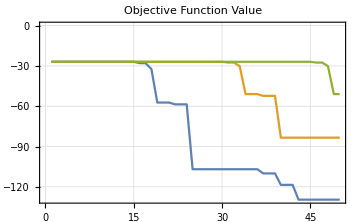
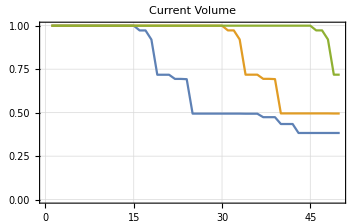
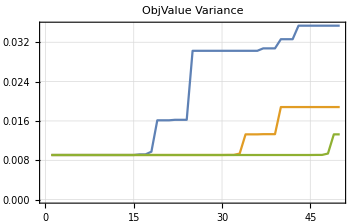
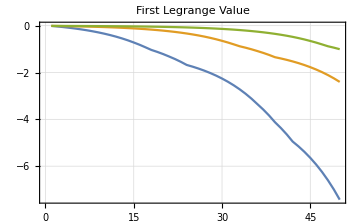
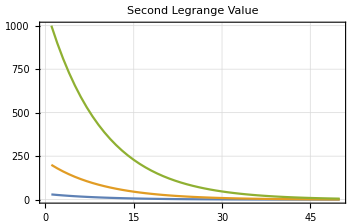
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
TableForm[{
{ListLinePlot[{data1[[2]],data2[[2]],data3[[2]]},PlotTheme->"Detailed",ImageSize->Medium,PlotRange->All,PlotLabel->"Objective Function Value"],ListLinePlot[{data1[[3]],data2[[3]],data3[[3]]},PlotTheme->"Detailed",ImageSize->Medium,PlotRange->All,PlotLabel->"Current Volume"],
ListLinePlot[{data1[[6]],data2[[6]],data3[[6]]},PlotTheme->"Detailed",ImageSize->Medium,PlotRange->All,PlotLabel->"ObjValue Variance"]},
{ListLinePlot[{data1[[4]],data2[[4]],data3[[4]]},PlotTheme->"Detailed",ImageSize->Medium,PlotRange->All,PlotLabel->"First Legrange Value"],ListLinePlot[{data1[[5]],data2[[5]],data3[[5]]},PlotTheme->"Detailed",ImageSize->Medium,PlotRange->All,PlotLabel->"Second Legrange Value"]}}]
```

changing of first Legrange coef

```mathematica
data4=toplevelset3D[30,16,16,0.3,3,3,0,50,0.90,-0.01,30.];
data5=toplevelset3D[30,16,16,0.3,3,3,0,50,0.90,-0.05,30.];
data6=toplevelset3D[30,16,16,0.3,3,3,0,50,0.90,-0.25,30.];
```

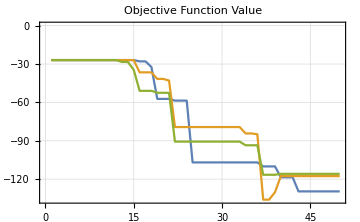
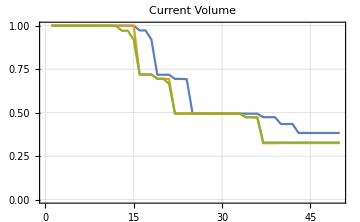
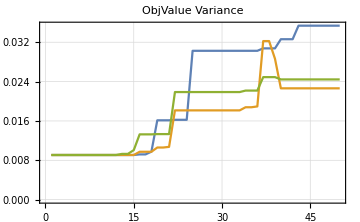
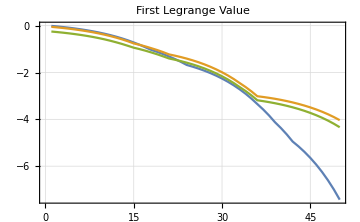
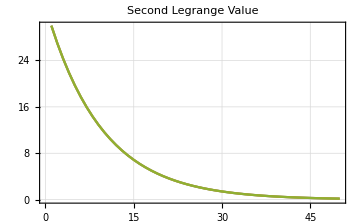
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
TableForm[{
{ListLinePlot[{data4[[2]],data5[[2]],data6[[2]]},PlotTheme->"Detailed",ImageSize->Medium,PlotLabel->"Objective Function Value"],ListLinePlot[{data4[[3]],data5[[3]],data6[[3]]},PlotTheme->"Detailed",ImageSize->Medium,PlotRange->All,PlotLabel->"Current Volume"],
ListLinePlot[{data4[[6]],data5[[6]],data6[[6]]},PlotTheme->"Detailed",PlotRange->All,ImageSize->Medium,PlotLabel->"ObjValue Variance"]},
{ListLinePlot[{data4[[4]],data5[[4]],data6[[4]]},PlotTheme->"Detailed",ImageSize->Medium,PlotRange->All,PlotLabel->"First Legrange Value"],ListLinePlot[{data4[[5]],data5[[5]],data6[[5]]},PlotTheme->"Detailed",ImageSize->Medium,PlotLabel->"Second Legrange Value"]}}]
```

changing of penalty factor

```mathematica
data7=toplevelset3D[30,16,16,0.3,3,3,0,50,0.85,-0.01,30.];
data8=toplevelset3D[30,16,16,0.3,3,3,0,50,0.90,-0.01,30.];
data9=toplevelset3D[30,16,16,0.3,3,3,0,50,0.95,-0.01,30.];
```

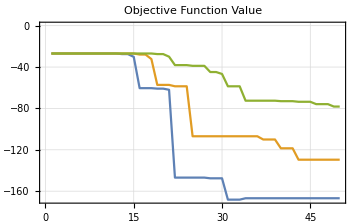
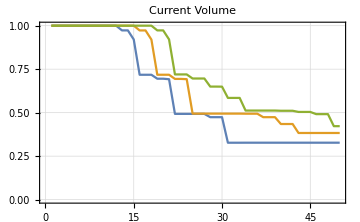
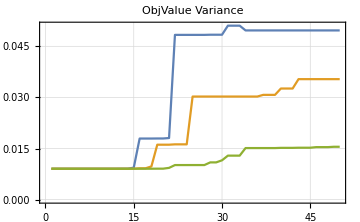
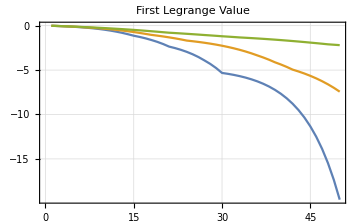
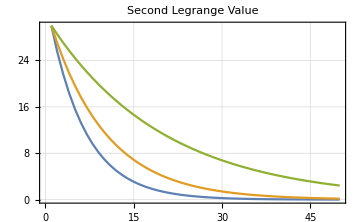
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
TableForm[{
{ListLinePlot[{data7[[2]],data8[[2]],data9[[2]]},PlotTheme->"Detailed",ImageSize->Medium,PlotLabel->"Objective Function Value"],ListLinePlot[{data7[[3]],data8[[3]],data9[[3]]},PlotTheme->"Detailed",ImageSize->Medium,PlotRange->All,PlotLabel->"Current Volume"],
ListLinePlot[{data7[[6]],data8[[6]],data9[[6]]},PlotTheme->"Detailed",PlotRange->All,ImageSize->Medium,PlotLabel->"ObjValue Variance"]},
{ListLinePlot[{data7[[4]],data8[[4]],data9[[4]]},PlotTheme->"Detailed",ImageSize->Medium,PlotRange->All,PlotLabel->"First Legrange Value"],ListLinePlot[{data7[[5]],data8[[5]],data9[[5]]},PlotTheme->"Detailed",ImageSize->Medium,PlotLabel->"Second Legrange Value"]}}]
```

```mathematica
data10=toplevelset3D[30,16,16,0.3,3,3,0,50,0.95,-0.01,30.];
data11=toplevelset3D[30,16,16,0.3,3.5,3,0,50,0.95,-0.01,30.];
data12=toplevelset3D[30,16,16,0.3,4,3,0,50,0.95,-0.01,30.];
```

```mathematica
data13=toplevelset3D[30,16,16,0.3,5,3,0,50,0.95,-0.01,30.];
data14=toplevelset3D[30,16,16,0.3,6,3,0,50,0.95,-0.01,30.];
data15=toplevelset3D[30,16,16,0.3,7,3,0,50,0.95,-0.01,30.];
```

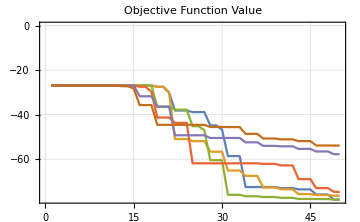
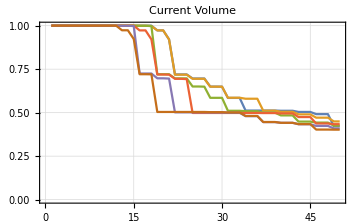
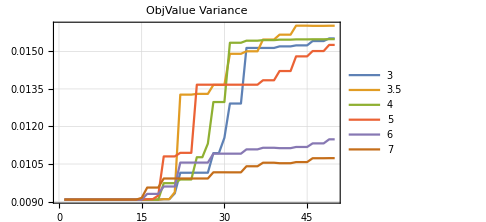
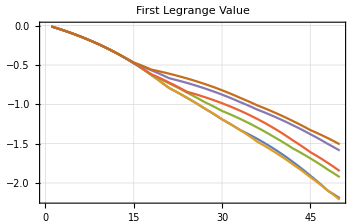
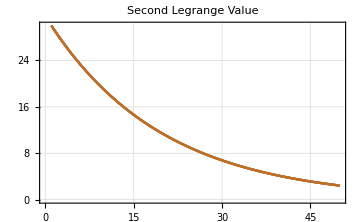
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
TableForm[{
{ListLinePlot[{data10[[2]],data11[[2]],data12[[2]],data13[[2]],data14[[2]],data15[[2]]},PlotTheme->"Detailed",ImageSize->Medium,PlotRange->All,PlotLabel->"Objective Function Value"],ListLinePlot[{data10[[3]],data11[[3]],data12[[3]],data13[[3]],data14[[3]],data15[[3]]},PlotTheme->"Detailed",ImageSize->Medium,PlotRange->All,PlotLabel->"Current Volume"],
ListLinePlot[{data10[[6]],data11[[6]],data12[[6]],data13[[6]],data14[[6]],data15[[6]]},PlotTheme->"Detailed",ImageSize->Medium,PlotRange->All,PlotLabel->"ObjValue Variance",PlotLegends->{"3","3.5","4","5","6","7"}]},
{ListLinePlot[{data10[[4]],data11[[4]],data12[[4]],data13[[4]],data14[[4]],data15[[4]]},PlotTheme->"Detailed",ImageSize->Medium,PlotRange->All,PlotLabel->"First Legrange Value"],ListLinePlot[{data10[[5]],data11[[5]],data12[[5]],data13[[5]],data14[[5]],data15[[5]]},PlotTheme->"Detailed",ImageSize->Medium,PlotRange->All,PlotLabel->"Second Legrange Value"]}}]
```

```mathematica
data16=toplevelset3D[30,16,16,0.3,7,3,0,50,0.95,-0.01,30.];
data17=toplevelset3D[30,16,16,0.3,7,5,0,50,0.95,-0.01,30.];
data18=toplevelset3D[30,16,16,0.3,7,7,0,50,0.95,-0.01,30.];
```

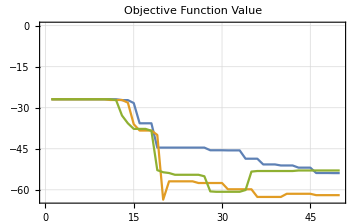
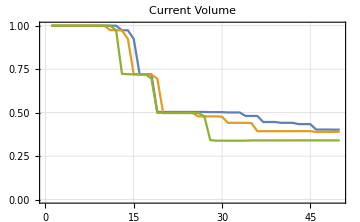
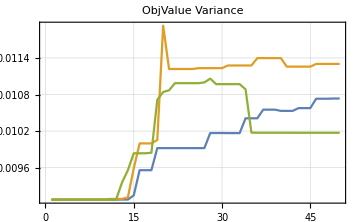
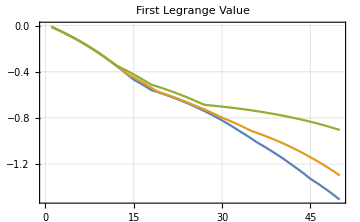
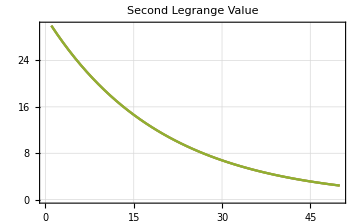
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
TableForm[{
{ListLinePlot[{data16[[2]],data17[[2]],data18[[2]]},PlotTheme->"Detailed",ImageSize->Medium,PlotLabel->"Objective Function Value"],ListLinePlot[{data16[[3]],data17[[3]],data18[[3]]},PlotTheme->"Detailed",ImageSize->Medium,PlotRange->All,PlotLabel->"Current Volume"],
ListLinePlot[{data16[[6]],data17[[6]],data18[[6]]},PlotTheme->"Detailed",PlotRange->All,ImageSize->Medium,PlotLabel->"ObjValue Variance"]},
{ListLinePlot[{data16[[4]],data17[[4]],data18[[4]]},PlotTheme->"Detailed",ImageSize->Medium,PlotRange->All,PlotLabel->"First Legrange Value"],ListLinePlot[{data16[[5]],data17[[5]],data18[[5]]},PlotTheme->"Detailed",ImageSize->Medium,PlotLabel->"Second Legrange Value"]}}]
```

```mathematica
data19=toplevelset3D[30,16,16,0.3,3,3,0,200,0.95,-0.01,30.,1];
data20=toplevelset3D[30,16,16,0.3,3,3,0,200,0.95,-0.01,30.,4];
data21=toplevelset3D[30,16,16,0.3,3,3,0,200,0.95,-0.01,30.,7];
```

4 iterations done

8 iterations done

12 iterations done

16 iterations done

20 iterations done

24 iterations done

28 iterations done

32 iterations done

36 iterations done

40 iterations done

44 iterations done

48 iterations done

52 iterations done

56 iterations done

60 iterations done

64 iterations done

68 iterations done

72 iterations done

76 iterations done

80 iterations done

84 iterations done

88 iterations done

92 iterations done

96 iterations done

100 iterations done

104 iterations done

108 iterations done

112 iterations done

116 iterations done

120 iterations done

124 iterations done

128 iterations done

132 iterations done

136 iterations done

140 iterations done

144 iterations done

148 iterations done

152 iterations done

156 iterations done

160 iterations done

164 iterations done

168 iterations done

172 iterations done

176 iterations done

180 iterations done

184 iterations done

188 iterations done

192 iterations done

196 iterations done

200 iterations done

==========================================

201 iterations done

30.3516 % volume

-94.8406 1st legrange parameter

0.00110693 2nd legrange parameter

4.41311 shapeSens max module

-Graphics3D-

4 iterations done

8 iterations done

12 iterations done

16 iterations done

20 iterations done

24 iterations done

28 iterations done

32 iterations done

36 iterations done

40 iterations done

44 iterations done

48 iterations done

52 iterations done

56 iterations done

60 iterations done

64 iterations done

68 iterations done

72 iterations done

76 iterations done

80 iterations done

84 iterations done

88 iterations done

92 iterations done

96 iterations done

100 iterations done

104 iterations done

108 iterations done

112 iterations done

116 iterations done

120 iterations done

124 iterations done

128 iterations done

132 iterations done

136 iterations done

140 iterations done

144 iterations done

148 iterations done

152 iterations done

156 iterations done

160 iterations done

164 iterations done

168 iterations done

172 iterations done

176 iterations done

180 iterations done

184 iterations done

188 iterations done

192 iterations done

196 iterations done

200 iterations done

==========================================

201 iterations done

30.2995 % volume

-68.0951 1st legrange parameter

0.00110693 2nd legrange parameter

4.89995 shapeSens max module

-Graphics3D-

4 iterations done

8 iterations done

12 iterations done

16 iterations done

20 iterations done

24 iterations done

28 iterations done

32 iterations done

36 iterations done

40 iterations done

44 iterations done

48 iterations done

52 iterations done

56 iterations done

60 iterations done

64 iterations done

68 iterations done

72 iterations done

76 iterations done

80 iterations done

84 iterations done

88 iterations done

92 iterations done

96 iterations done

100 iterations done

104 iterations done

108 iterations done

112 iterations done

116 iterations done

120 iterations done

124 iterations done

128 iterations done

132 iterations done

136 iterations done

==========================================

139 iterations done

29.987 % volume

-20.6096 1st legrange parameter

0.0266229 2nd legrange parameter

4.7058 shapeSens max module

-Graphics3D-

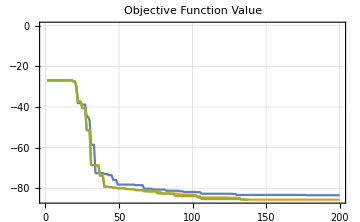
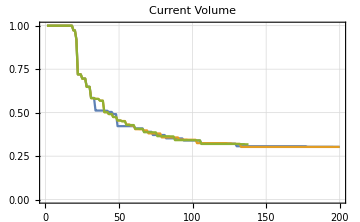
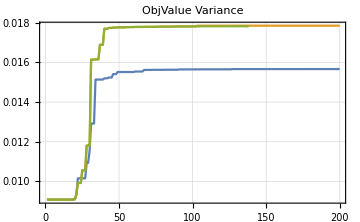
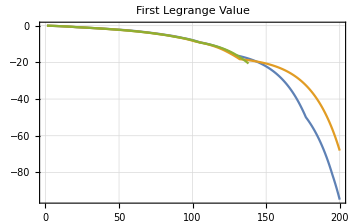
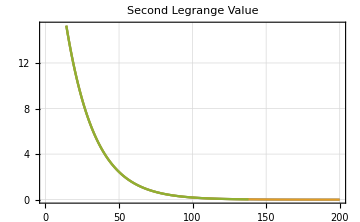
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
TableForm[{
{ListLinePlot[{data19[[2]],data20[[2]],data21[[2]]},PlotTheme->"Detailed",ImageSize->Medium,PlotLabel->"Objective Function Value"],ListLinePlot[{data19[[3]],data20[[3]],data21[[3]]},PlotTheme->"Detailed",ImageSize->Medium,PlotRange->All,PlotLabel->"Current Volume"],
ListLinePlot[{data19[[6]],data20[[6]],data21[[6]]},PlotTheme->"Detailed",PlotRange->All,ImageSize->Medium,PlotLabel->"ObjValue Variance"]},
{ListLinePlot[{data19[[4]],data20[[4]],data21[[4]]},PlotTheme->"Detailed",ImageSize->Medium,PlotRange->All,PlotLabel->"First Legrange Value"],ListLinePlot[{data19[[5]],data20[[5]],data21[[5]]},PlotTheme->"Detailed",ImageSize->Medium,PlotLabel->"Second Legrange Value"]}}]
```

```mathematica
data19=toplevelset3D[20,10,10,0.3,5,5,0,100,0.9,-1,1000.,2];
```

4 iterations done

-Graphics3D-

4.60146 shapeSens max module

-Graphics3D-

4.30605 shapeSens max module

-Graphics3D-

8 iterations done

-Graphics3D-

4.67281 shapeSens max module

-Graphics3D-

4.53169 shapeSens max module

-Graphics3D-

12 iterations done

-Graphics3D-

4.67281 shapeSens max module

-Graphics3D-

4.53239 shapeSens max module

-Graphics3D-

16 iterations done

-Graphics3D-

4.67281 shapeSens max module

-Graphics3D-

4.53239 shapeSens max module

-Graphics3D-

20 iterations done

-Graphics3D-

4.67281 shapeSens max module

-Graphics3D-

4.53239 shapeSens max module

-Graphics3D-

24 iterations done

-Graphics3D-

4.67281 shapeSens max module

-Graphics3D-

4.48591 shapeSens max module

-Graphics3D-

28 iterations done

-Graphics3D-

4.68088 shapeSens max module

-Graphics3D-

4.48224 shapeSens max module

-Graphics3D-

32 iterations done

-Graphics3D-

4.73304 shapeSens max module

-Graphics3D-

4.59126 shapeSens max module

-Graphics3D-

36 iterations done

-Graphics3D-

4.73304 shapeSens max module

-Graphics3D-

4.59126 shapeSens max module

-Graphics3D-

40 iterations done

-Graphics3D-

4.73304 shapeSens max module

-Graphics3D-

4.59126 shapeSens max module

-Graphics3D-

44 iterations done

-Graphics3D-

4.73304 shapeSens max module

-Graphics3D-

4.54433 shapeSens max module

-Graphics3D-

48 iterations done

-Graphics3D-

4.79401 shapeSens max module

-Graphics3D-

4.61247 shapeSens max module

-Graphics3D-

52 iterations done

-Graphics3D-

4.80378 shapeSens max module

-Graphics3D-

4.70597 shapeSens max module

-Graphics3D-

56 iterations done

-Graphics3D-

4.80378 shapeSens max module

-Graphics3D-

4.70597 shapeSens max module

-Graphics3D-

60 iterations done

-Graphics3D-

4.80378 shapeSens max module

-Graphics3D-

4.70597 shapeSens max module

-Graphics3D-

64 iterations done

-Graphics3D-

4.80378 shapeSens max module

-Graphics3D-

4.6736 shapeSens max module

-Graphics3D-

68 iterations done

-Graphics3D-

4.80378 shapeSens max module

-Graphics3D-

4.61318 shapeSens max module

-Graphics3D-

72 iterations done

-Graphics3D-

4.86606 shapeSens max module

-Graphics3D-

4.84672 shapeSens max module

-Graphics3D-

76 iterations done

-Graphics3D-

4.86606 shapeSens max module

-Graphics3D-

4.84672 shapeSens max module

-Graphics3D-

80 iterations done

-Graphics3D-

4.86606 shapeSens max module

-Graphics3D-

4.84672 shapeSens max module

-Graphics3D-

84 iterations done

-Graphics3D-

4.86606 shapeSens max module

-Graphics3D-

4.84031 shapeSens max module

-Graphics3D-

88 iterations done

-Graphics3D-

4.86606 shapeSens max module

-Graphics3D-

4.82837 shapeSens max module

-Graphics3D-

92 iterations done

-Graphics3D-

4.86606 shapeSens max module

-Graphics3D-

4.81087 shapeSens max module

-Graphics3D-

96 iterations done

-Graphics3D-

4.86606 shapeSens max module

-Graphics3D-

4.78526 shapeSens max module

-Graphics3D-

100 iterations done

-Graphics3D-

4.86606 shapeSens max module

-Graphics3D-

4.74775 shapeSens max module

-Graphics3D-

==========================================

101 iterations done

30.65 % volume

-18.2012 1st legrange parameter

0.0295127 2nd legrange parameter

4.74775 shapeSens max module

-Graphics3D-

```mathematica
data19[[2]]
```

{-30.2939,-30.2939,-30.2939,-30.7677,-35.057,-41.0025,-41.0025,-41.0025,-41.0025,-41.0025,-41.003,-41.003,-41.003,-41.003,-41.003,-41.003,-41.003,-41.003,-41.003,-41.003,-41.003,-41.003,-41.003,-41.003,-41.003,-41.5501,-41.5501,-41.5501,-41.5501,-42.002,-44.0055,-44.0055,-44.0055,-44.0055,-44.0055,-44.0055,-44.0055,-44.0055,-44.0055,-44.0055,-44.0055,-44.0055,-44.0055,-44.0055,-44.0055,-46.4619,-46.4619,-46.4619,-46.4619,-46.4866,-50.3956,-50.3956,-50.3956,-50.3956,-50.3956,-50.3956,-50.3956,-50.3956,-50.3956,-50.3956,-50.3956,-50.3956,-50.3956,-50.3956,-50.3956,-50.3956,-50.3956,-50.3956,-50.3956,-50.4338,-55.0793,-55.0793,-55.0793,-55.0793,-55.0793,-55.0793,-55.0793,-55.0793,-55.0793,-55.0793,-55.0793,-55.0793,-55.0793,-55.0793,-55.0793,-55.0793,-55.0793,-55.0793,-55.0793,-55.0793,-55.0793,-55.0793,-55.0793,-55.0793,-55.0793,-55.0793,-55.0793,-55.0793,-55.0793,-55.0793}

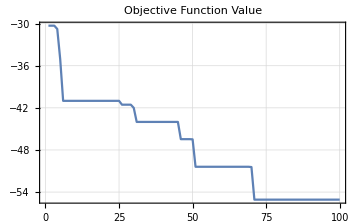
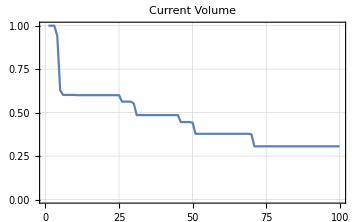
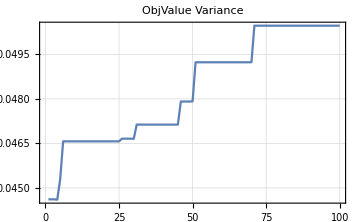

```mathematica
{ListLinePlot[{data19[[2]]},PlotTheme->"Detailed",ImageSize->Medium,PlotLabel->"Objective Function Value"],ListLinePlot[{data19[[3]]},PlotTheme->"Detailed",ImageSize->Medium,PlotRange->All,PlotLabel->"Current Volume"],
ListLinePlot[{data19[[6]]},PlotTheme->"Detailed",PlotRange->All,ImageSize->Medium,PlotLabel->"ObjValue Variance"]}
```

```mathematica
data20=toplevelset3D[40,20,20,0.3,5,5,0,100,0.9,-1,1000.,2];
```

4 iterations done

-Graphics3D-

4.6259 shapeSens max module

-Graphics3D-

4.31009 shapeSens max module

-Graphics3D-

8 iterations done

-Graphics3D-

4.75621 shapeSens max module

-Graphics3D-

4.53162 shapeSens max module

-Graphics3D-

12 iterations done

-Graphics3D-

4.77817 shapeSens max module

-Graphics3D-

4.64271 shapeSens max module

-Graphics3D-

16 iterations done

-Graphics3D-

4.77817 shapeSens max module

-Graphics3D-

4.64271 shapeSens max module

-Graphics3D-

20 iterations done

-Graphics3D-

4.77817 shapeSens max module

-Graphics3D-

4.64271 shapeSens max module

-Graphics3D-

24 iterations done

-Graphics3D-

4.77817 shapeSens max module

-Graphics3D-

4.59787 shapeSens max module

-Graphics3D-

28 iterations done

-Graphics3D-

4.79889 shapeSens max module

-Graphics3D-

4.58906 shapeSens max module

-Graphics3D-

32 iterations done

-Graphics3D-

4.84913 shapeSens max module

-Graphics3D-

4.65755 shapeSens max module

-Graphics3D-

36 iterations done

-Graphics3D-

4.85068 shapeSens max module

-Graphics3D-

4.68745 shapeSens max module

-Graphics3D-

40 iterations done

-Graphics3D-

4.85068 shapeSens max module

-Graphics3D-

4.68745 shapeSens max module

-Graphics3D-

44 iterations done

-Graphics3D-

4.89714 shapeSens max module

-Graphics3D-

4.73546 shapeSens max module

-Graphics3D-

48 iterations done

-Graphics3D-

4.89464 shapeSens max module

-Graphics3D-

4.73679 shapeSens max module

-Graphics3D-

52 iterations done

-Graphics3D-

4.90206 shapeSens max module

-Graphics3D-

4.74895 shapeSens max module

-Graphics3D-

56 iterations done

-Graphics3D-

4.90639 shapeSens max module

-Graphics3D-

4.75897 shapeSens max module

-Graphics3D-

60 iterations done

-Graphics3D-

4.90639 shapeSens max module

-Graphics3D-

4.75897 shapeSens max module

-Graphics3D-

64 iterations done

-Graphics3D-

4.90639 shapeSens max module

-Graphics3D-

4.75912 shapeSens max module

-Graphics3D-

68 iterations done

-Graphics3D-

4.90639 shapeSens max module

-Graphics3D-

4.75912 shapeSens max module

-Graphics3D-

72 iterations done

-Graphics3D-

4.90639 shapeSens max module

-Graphics3D-

4.74439 shapeSens max module

-Graphics3D-

76 iterations done

-Graphics3D-

4.8747 shapeSens max module

-Graphics3D-

4.69216 shapeSens max module

-Graphics3D-

80 iterations done

-Graphics3D-

4.91227 shapeSens max module

-Graphics3D-

4.73015 shapeSens max module

-Graphics3D-

84 iterations done

-Graphics3D-

4.93732 shapeSens max module

-Graphics3D-

4.81399 shapeSens max module

-Graphics3D-

88 iterations done

-Graphics3D-

4.93732 shapeSens max module

-Graphics3D-

4.81399 shapeSens max module

-Graphics3D-

92 iterations done

-Graphics3D-

4.93732 shapeSens max module

-Graphics3D-

4.80165 shapeSens max module

-Graphics3D-

96 iterations done

-Graphics3D-

4.91502 shapeSens max module

-Graphics3D-

4.71844 shapeSens max module

-Graphics3D-

100 iterations done

-Graphics3D-

4.93986 shapeSens max module

-Graphics3D-

4.76381 shapeSens max module

-Graphics3D-

==========================================

101 iterations done

34.0125 % volume

-2.0635 1st legrange parameter

0.0295127 2nd legrange parameter

4.76381 shapeSens max module

-Graphics3D-

```mathematica
data20=toplevelset3D[40,20,20,0.3,5,5,0,200,0.9,-1,1000.,2];
```

4 iterations done

-Graphics3D-

4.6259 shapeSens max module

-Graphics3D-

4.31009 shapeSens max module

-Graphics3D-

8 iterations done

-Graphics3D-

4.75621 shapeSens max module

-Graphics3D-

4.53162 shapeSens max module

-Graphics3D-

12 iterations done

-Graphics3D-

4.77817 shapeSens max module

-Graphics3D-

4.64271 shapeSens max module

-Graphics3D-

16 iterations done

-Graphics3D-

4.7989 shapeSens max module

-Graphics3D-

4.56422 shapeSens max module

-Graphics3D-

20 iterations done

-Graphics3D-

4.80174 shapeSens max module

-Graphics3D-

4.5357 shapeSens max module

-Graphics3D-

24 iterations done

-Graphics3D-

4.80213 shapeSens max module

-Graphics3D-

4.65328 shapeSens max module

-Graphics3D-

28 iterations done

-Graphics3D-

4.97533 shapeSens max module

-Graphics3D-

4.82104 shapeSens max module

-Graphics3D-

32 iterations done

-Graphics3D-

5.0527 shapeSens max module

-Graphics3D-

4.80856 shapeSens max module

-Graphics3D-

36 iterations done

-Graphics3D-

5.16884 shapeSens max module

-Graphics3D-

5.1625 shapeSens max module

-Graphics3D-

40 iterations done

-Graphics3D-

5.08271 shapeSens max module

-Graphics3D-

5.0728 shapeSens max module

-Graphics3D-

44 iterations done

-Graphics3D-

5.24683 shapeSens max module

-Graphics3D-

5.2325 shapeSens max module

-Graphics3D-

48 iterations done

-Graphics3D-

5.25673 shapeSens max module

-Graphics3D-

5.23564 shapeSens max module

-Graphics3D-

52 iterations done

-Graphics3D-

5.25673 shapeSens max module

-Graphics3D-

5.21299 shapeSens max module

-Graphics3D-

56 iterations done

-Graphics3D-

5.25673 shapeSens max module

-Graphics3D-

5.16604 shapeSens max module

-Graphics3D-

60 iterations done

-Graphics3D-

5.25673 shapeSens max module

-Graphics3D-

5.06868 shapeSens max module

-Graphics3D-

64 iterations done

-Graphics3D-

5.25673 shapeSens max module

-Graphics3D-

5.07259 shapeSens max module

-Graphics3D-

==========================================

65 iterations done

29.0813 % volume

-86.6544 1st legrange parameter

1.31002 2nd legrange parameter

5.07259 shapeSens max module

-Graphics3D-

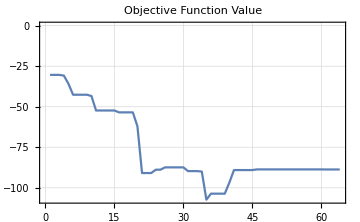
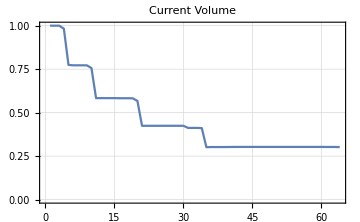
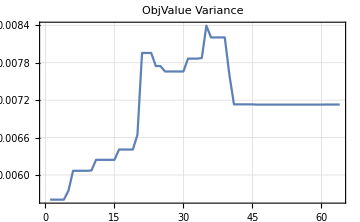

```mathematica
{ListLinePlot[{data20[[2]]},PlotTheme->"Detailed",ImageSize->Medium,PlotLabel->"Objective Function Value"],ListLinePlot[{data20[[3]]},PlotTheme->"Detailed",ImageSize->Medium,PlotRange->All,PlotLabel->"Current Volume"],
ListLinePlot[{data20[[6]]},PlotTheme->"Detailed",PlotRange->All,ImageSize->Medium,PlotLabel->"ObjValue Variance"]}
```

```mathematica
data20=toplevelset3D[20,10,10,0.2,5,5,0,200,0.9,-1,1000.,2];
```

4 iterations done

-Graphics3D-

5.38979 shapeSens max module

-Graphics3D-

4.96938 shapeSens max module

-Graphics3D-

8 iterations done

-Graphics3D-

5.2421 shapeSens max module

-Graphics3D-

4.84213 shapeSens max module

-Graphics3D-

12 iterations done

-Graphics3D-

5.10056 shapeSens max module

-Graphics3D-

4.96998 shapeSens max module

-Graphics3D-

16 iterations done

-Graphics3D-

5.39848 shapeSens max module

-Graphics3D-

5.15593 shapeSens max module

-Graphics3D-

20 iterations done

-Graphics3D-

5.463 shapeSens max module

-Graphics3D-

5.25796 shapeSens max module

-Graphics3D-

==========================================

21 iterations done

19.8 % volume

-2.26562 1st legrange parameter

135.085 2nd legrange parameter

5.25796 shapeSens max module

-Graphics3D-

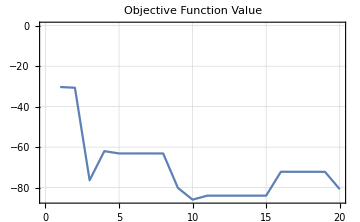
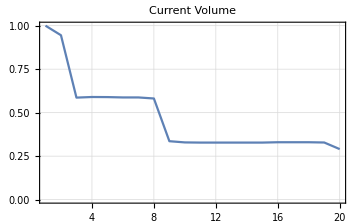
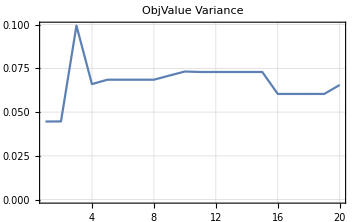

```mathematica
{ListLinePlot[{data20[[2]]},PlotTheme->"Detailed",ImageSize->Medium,PlotLabel->"Objective Function Value"],ListLinePlot[{data20[[3]]},PlotTheme->"Detailed",ImageSize->Medium,PlotRange->All,PlotLabel->"Current Volume"],
ListLinePlot[{data20[[6]]},PlotTheme->"Detailed",PlotRange->All,ImageSize->Medium,PlotLabel->"ObjValue Variance"]}
```

```mathematica
data20=toplevelset3D[20,10,10,0.1,5,5,0,200,0.9,-1,1000.,2];
```

4 iterations done

-Graphics3D-

5.09226 shapeSens max module

-Graphics3D-

4.59322 shapeSens max module

-Graphics3D-

8 iterations done

-Graphics3D-

5.78347 shapeSens max module

-Graphics3D-

5.22074 shapeSens max module

-Graphics3D-

12 iterations done

-Graphics3D-

6.00788 shapeSens max module

-Graphics3D-

5.74533 shapeSens max module

-Graphics3D-

16 iterations done

-Graphics3D-

6.40528 shapeSens max module

-Graphics3D-

6.03449 shapeSens max module

-Graphics3D-

20 iterations done

-Graphics3D-

6.60139 shapeSens max module

-Graphics3D-

6.28998 shapeSens max module

-Graphics3D-

24 iterations done

-Graphics3D-

7.15242 shapeSens max module

-Graphics3D-

6.93737 shapeSens max module

-Graphics3D-

28 iterations done

-Graphics3D-

7.5002 shapeSens max module

-Graphics3D-

7.16875 shapeSens max module

-Graphics3D-

32 iterations done

-Graphics3D-

7.78286 shapeSens max module

-Graphics3D-

7.41809 shapeSens max module

-Graphics3D-

36 iterations done

-Graphics3D-

8.04602 shapeSens max module

-Graphics3D-

7.64249 shapeSens max module

-Graphics3D-

40 iterations done

-Graphics3D-

8.07396 shapeSens max module

-Graphics3D-

7.51965 shapeSens max module

-Graphics3D-

44 iterations done

-Graphics3D-

8.36324 shapeSens max module

-Graphics3D-

7.89794 shapeSens max module

-Graphics3D-

48 iterations done

-Graphics3D-

8.45139 shapeSens max module

-Graphics3D-

7.98481 shapeSens max module

-Graphics3D-

52 iterations done

-Graphics3D-

8.91903 shapeSens max module

-Graphics3D-

8.8036 shapeSens max module

-Graphics3D-

56 iterations done

-Graphics3D-

8.60795 shapeSens max module

-Graphics3D-

8.2642 shapeSens max module

-Graphics3D-

60 iterations done

-Graphics3D-

8.67848 shapeSens max module

-Graphics3D-

8.20714 shapeSens max module

-Graphics3D-

64 iterations done

-Graphics3D-

8.73653 shapeSens max module

-Graphics3D-

8.23412 shapeSens max module

-Graphics3D-

68 iterations done

-Graphics3D-

10.4231 shapeSens max module

-Graphics3D-

10.3081 shapeSens max module

-Graphics3D-

72 iterations done

-Graphics3D-

10.7915 shapeSens max module

-Graphics3D-

10.2768 shapeSens max module

-Graphics3D-

```mathematica
data20=toplevelset3D[30,16,16,0.2,5,5,0,200,0.9,-1,1000.,2];
```

4 iterations done

-Graphics3D-

5.03538 shapeSens max module

-Graphics3D-

4.51414 shapeSens max module

-Graphics3D-

8 iterations done

-Graphics3D-

4.98 shapeSens max module

-Graphics3D-

4.46669 shapeSens max module

-Graphics3D-

12 iterations done

-Graphics3D-

4.96328 shapeSens max module

-Graphics3D-

4.67052 shapeSens max module

-Graphics3D-

16 iterations done

-Graphics3D-

5.3016 shapeSens max module

-Graphics3D-

5.10577 shapeSens max module

-Graphics3D-

20 iterations done

-Graphics3D-

5.15892 shapeSens max module

-Graphics3D-

4.88423 shapeSens max module

-Graphics3D-

24 iterations done

-Graphics3D-

4.98488 shapeSens max module

-Graphics3D-

4.70417 shapeSens max module

-Graphics3D-

28 iterations done

-Graphics3D-

5.02306 shapeSens max module

-Graphics3D-

4.9758 shapeSens max module

-Graphics3D-

32 iterations done

-Graphics3D-

4.81128 shapeSens max module

-Graphics3D-

4.74017 shapeSens max module

-Graphics3D-

36 iterations done

-Graphics3D-

4.91383 shapeSens max module

-Graphics3D-

4.78453 shapeSens max module

-Graphics3D-

40 iterations done

-Graphics3D-

4.91383 shapeSens max module

-Graphics3D-

4.72763 shapeSens max module

-Graphics3D-

44 iterations done

-Graphics3D-

4.9104 shapeSens max module

-Graphics3D-

4.7799 shapeSens max module

-Graphics3D-

48 iterations done

-Graphics3D-

4.9584 shapeSens max module

-Graphics3D-

4.98132 shapeSens max module

-Graphics3D-

==========================================

50 iterations done

19.9349 % volume

-26.4018 1st legrange parameter

6.36269 2nd legrange parameter

4.9859 shapeSens max module

-Graphics3D-

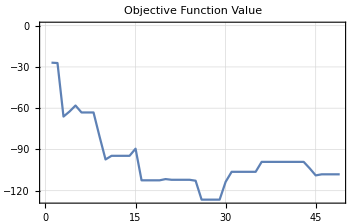
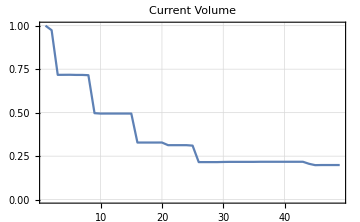
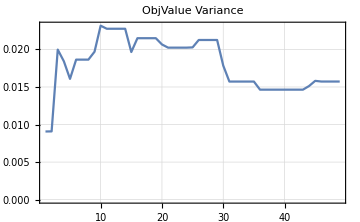

```mathematica
{ListLinePlot[{data20[[2]]},PlotTheme->"Detailed",ImageSize->Medium,PlotLabel->"Objective Function Value"],ListLinePlot[{data20[[3]]},PlotTheme->"Detailed",ImageSize->Medium,PlotRange->All,PlotLabel->"Current Volume"],
ListLinePlot[{data20[[6]]},PlotTheme->"Detailed",PlotRange->All,ImageSize->Medium,PlotLabel->"ObjValue Variance"]}
```

```mathematica
data20=toplevelset3D[30,16,16,0.2,3,3,0,200,0.9,-1,1000.,1];
```

4 iterations done

-Graphics3D-

5.03538 shapeSens max module

-Graphics3D-

4.51388 shapeSens max module

-Graphics3D-

8 iterations done

-Graphics3D-

5.03538 shapeSens max module

-Graphics3D-

4.5144 shapeSens max module

-Graphics3D-

12 iterations done

-Graphics3D-

5.03538 shapeSens max module

-Graphics3D-

4.51598 shapeSens max module

-Graphics3D-

16 iterations done

-Graphics3D-

5.0395 shapeSens max module

-Graphics3D-

4.32893 shapeSens max module

-Graphics3D-

20 iterations done

-Graphics3D-

5.18477 shapeSens max module

-Graphics3D-

4.52546 shapeSens max module

-Graphics3D-

24 iterations done

-Graphics3D-

5.19496 shapeSens max module

-Graphics3D-

4.62748 shapeSens max module

-Graphics3D-

28 iterations done

-Graphics3D-

5.4089 shapeSens max module

-Graphics3D-

4.89805 shapeSens max module

-Graphics3D-

32 iterations done

-Graphics3D-

5.45282 shapeSens max module

-Graphics3D-

4.86027 shapeSens max module

-Graphics3D-

36 iterations done

-Graphics3D-

5.43696 shapeSens max module

-Graphics3D-

4.99558 shapeSens max module

-Graphics3D-

40 iterations done

-Graphics3D-

5.11123 shapeSens max module

-Graphics3D-

4.78405 shapeSens max module

-Graphics3D-

44 iterations done

-Graphics3D-

5.11123 shapeSens max module

-Graphics3D-

4.64008 shapeSens max module

-Graphics3D-

48 iterations done

-Graphics3D-

5.15684 shapeSens max module

-Graphics3D-

4.29529 shapeSens max module

-Graphics3D-

52 iterations done

-Graphics3D-

6.77835 shapeSens max module

-Graphics3D-

7.47545 shapeSens max module

-Graphics3D-

56 iterations done

-Graphics3D-

8.00426 shapeSens max module

-Graphics3D-

8.91437 shapeSens max module

-Graphics3D-

60 iterations done

-Graphics3D-

8.25191 shapeSens max module

-Graphics3D-

8.91557 shapeSens max module

-Graphics3D-

64 iterations done

-Graphics3D-

8.40601 shapeSens max module

-Graphics3D-

9.25364 shapeSens max module

-Graphics3D-

68 iterations done

-Graphics3D-

8.71812 shapeSens max module

-Graphics3D-

9.39703 shapeSens max module

-Graphics3D-

72 iterations done

-Graphics3D-

8.71257 shapeSens max module

-Graphics3D-

9.51421 shapeSens max module

-Graphics3D-

76 iterations done

-Graphics3D-

8.6849 shapeSens max module

-Graphics3D-

8.97258 shapeSens max module

-Graphics3D-

80 iterations done

-Graphics3D-

8.6849 shapeSens max module

-Graphics3D-

9.09916 shapeSens max module

-Graphics3D-

84 iterations done

-Graphics3D-

8.6849 shapeSens max module

-Graphics3D-

9.5439 shapeSens max module

-Graphics3D-

==========================================

88 iterations done

20.0911 % volume

-495.779 1st legrange parameter

0.116106 2nd legrange parameter

9.60617 shapeSens max module

-Graphics3D-

```mathematica
data20=toplevelset3D[30,16,16,0.2,5,5,0,200,0.9,-1,1000.,2];
```

4 iterations done

-Graphics3D-

4.37487 shapeSens max module

-Graphics3D-

3.92143 shapeSens max module

-Graphics3D-

8 iterations done

-Graphics3D-

4.36823 shapeSens max module

-Graphics3D-

4.1091 shapeSens max module

-Graphics3D-

12 iterations done

-Graphics3D-

4.40634 shapeSens max module

-Graphics3D-

4.29205 shapeSens max module

-Graphics3D-

16 iterations done

-Graphics3D-

4.40616 shapeSens max module

-Graphics3D-

4.25745 shapeSens max module

-Graphics3D-

20 iterations done

-Graphics3D-

4.4048 shapeSens max module

-Graphics3D-

4.20452 shapeSens max module

-Graphics3D-

24 iterations done

-Graphics3D-

4.39625 shapeSens max module

-Graphics3D-

4.33814 shapeSens max module

-Graphics3D-

28 iterations done

-Graphics3D-

4.24599 shapeSens max module

-Graphics3D-

4.16041 shapeSens max module

-Graphics3D-

32 iterations done

-Graphics3D-

4.24599 shapeSens max module

-Graphics3D-

4.06853 shapeSens max module

-Graphics3D-

36 iterations done

-Graphics3D-

4.28382 shapeSens max module

-Graphics3D-

4.26949 shapeSens max module

-Graphics3D-

40 iterations done

-Graphics3D-

4.28382 shapeSens max module

-Graphics3D-

4.26319 shapeSens max module

-Graphics3D-

44 iterations done

-Graphics3D-

4.26999 shapeSens max module

-Graphics3D-

4.23052 shapeSens max module

-Graphics3D-

48 iterations done

-Graphics3D-

4.26999 shapeSens max module

-Graphics3D-

4.18814 shapeSens max module

-Graphics3D-

52 iterations done

-Graphics3D-

4.26999 shapeSens max module

-Graphics3D-

4.10027 shapeSens max module

-Graphics3D-

==========================================

54 iterations done

19.974 % volume

-97.7619 1st legrange parameter

4.17456 2nd legrange parameter

4.06632 shapeSens max module

-Graphics3D-

```mathematica
data20=toplevelset3D[30,16,16,0.2,5,5,0,200,0.9,-1,1000.,2];
```

4 iterations done

-Graphics3D-

4.28518 shapeSens max module

-Graphics3D-

4.06133 shapeSens max module

-Graphics3D-

8 iterations done

-Graphics3D-

4.28518 shapeSens max module

-Graphics3D-

4.0649 shapeSens max module

-Graphics3D-

12 iterations done

-Graphics3D-

4.26719 shapeSens max module

-Graphics3D-

4.25407 shapeSens max module

-Graphics3D-

16 iterations done

-Graphics3D-

4.13641 shapeSens max module

-Graphics3D-

4.11594 shapeSens max module

-Graphics3D-

20 iterations done

-Graphics3D-

4.13641 shapeSens max module

-Graphics3D-

4.10693 shapeSens max module

-Graphics3D-

24 iterations done

-Graphics3D-

4.09535 shapeSens max module

-Graphics3D-

4.05204 shapeSens max module

-Graphics3D-

28 iterations done

-Graphics3D-

4.09535 shapeSens max module

-Graphics3D-

4.00555 shapeSens max module

-Graphics3D-

32 iterations done

-Graphics3D-

4.10952 shapeSens max module

-Graphics3D-

4.01791 shapeSens max module

-Graphics3D-

36 iterations done

-Graphics3D-

4.23298 shapeSens max module

-Graphics3D-

5.0482 shapeSens max module

-Graphics3D-

40 iterations done

-Graphics3D-

4.25277 shapeSens max module

-Graphics3D-

3.98659 shapeSens max module

-Graphics3D-

44 iterations done

-Graphics3D-

4.24545 shapeSens max module

-Graphics3D-

3.55456 shapeSens max module

-Graphics3D-

48 iterations done

-Graphics3D-

4.24765 shapeSens max module

-Graphics3D-

3.99405 shapeSens max module

-Graphics3D-

52 iterations done

-Graphics3D-

4.03337 shapeSens max module

-Graphics3D-

5.54809 shapeSens max module

-Graphics3D-

56 iterations done

-Graphics3D-

4.06728 shapeSens max module

-Graphics3D-

4.22785 shapeSens max module

-Graphics3D-

60 iterations done

-Graphics3D-

4.07302 shapeSens max module

-Graphics3D-

4.07772 shapeSens max module

-Graphics3D-

64 iterations done

-Graphics3D-

4.0678 shapeSens max module

-Graphics3D-

4.01704 shapeSens max module

-Graphics3D-

68 iterations done

-Graphics3D-

4.0678 shapeSens max module

-Graphics3D-

3.96254 shapeSens max module

-Graphics3D-

72 iterations done

-Graphics3D-

4.0683 shapeSens max module

-Graphics3D-

4.10199 shapeSens max module

-Graphics3D-

76 iterations done

-Graphics3D-

4.0614 shapeSens max module

-Graphics3D-

4.09627 shapeSens max module

-Graphics3D-

80 iterations done

-Graphics3D-

4.0614 shapeSens max module

-Graphics3D-

4.11162 shapeSens max module

-Graphics3D-

84 iterations done

-Graphics3D-

4.0614 shapeSens max module

-Graphics3D-

4.16552 shapeSens max module

-Graphics3D-

88 iterations done

-Graphics3D-

4.12327 shapeSens max module

-Graphics3D-

31.8269 shapeSens max module

-Graphics3D-

92 iterations done

-Graphics3D-

4.02791 shapeSens max module

-Graphics3D-

16.3698 shapeSens max module

-Graphics3D-

96 iterations done

-Graphics3D-

4.02682 shapeSens max module

-Graphics3D-

9.66271 shapeSens max module

-Graphics3D-

100 iterations done

-Graphics3D-

4.03418 shapeSens max module

-Graphics3D-

12.0763 shapeSens max module

-Graphics3D-

104 iterations done

-Graphics3D-

6.84317 shapeSens max module

-Graphics3D-

61.1581 shapeSens max module

-Graphics3D-

108 iterations done

-Graphics3D-

4.05089 shapeSens max module

-Graphics3D-

13.0105 shapeSens max module

-Graphics3D-

112 iterations done

-Graphics3D-

4.10237 shapeSens max module

-Graphics3D-

32.8772 shapeSens max module

-Graphics3D-

$Aborted

```mathematica
data20=toplevelset3D[20,10,10,0.2,3,3,0,200,0.9,-1,1000.,2];
```

4 iterations done

-Graphics3D-

36.9 % volume

8.68017 shapeSens max module

-Graphics3D-

8.38678 shapeSens max module

-Graphics3D-

8 iterations done

-Graphics3D-

36.9 % volume

8.68017 shapeSens max module

-Graphics3D-

8.38678 shapeSens max module

-Graphics3D-

12 iterations done

-Graphics3D-

36.9 % volume

8.68017 shapeSens max module

-Graphics3D-

8.35744 shapeSens max module

-Graphics3D-

16 iterations done

-Graphics3D-

36.9 % volume

8.68017 shapeSens max module

-Graphics3D-

8.20766 shapeSens max module

-Graphics3D-

20 iterations done

-Graphics3D-

36.15 % volume

8.68389 shapeSens max module

-Graphics3D-

8.08264 shapeSens max module

-Graphics3D-

24 iterations done

-Graphics3D-

31.05 % volume

8.60475 shapeSens max module

-Graphics3D-

8.19711 shapeSens max module

-Graphics3D-

28 iterations done

-Graphics3D-

31.05 % volume

8.60475 shapeSens max module

-Graphics3D-

8.15635 shapeSens max module

-Graphics3D-

32 iterations done

-Graphics3D-

31. % volume

8.60414 shapeSens max module

-Graphics3D-

8.01006 shapeSens max module

-Graphics3D-

36 iterations done

-Graphics3D-

27.85 % volume

9.12473 shapeSens max module

-Graphics3D-

8.67512 shapeSens max module

-Graphics3D-

40 iterations done

-Graphics3D-

27.85 % volume

9.12473 shapeSens max module

-Graphics3D-

8.63016 shapeSens max module

-Graphics3D-

44 iterations done

-Graphics3D-

27.3 % volume

9.13236 shapeSens max module

-Graphics3D-

8.5197 shapeSens max module

-Graphics3D-

48 iterations done

-Graphics3D-

26.45 % volume

9.08578 shapeSens max module

-Graphics3D-

8.54722 shapeSens max module

-Graphics3D-

52 iterations done

-Graphics3D-

26.3 % volume

9.08594 shapeSens max module

-Graphics3D-

8.55989 shapeSens max module

-Graphics3D-

56 iterations done

-Graphics3D-

26.3 % volume

9.08594 shapeSens max module

-Graphics3D-

8.44942 shapeSens max module

-Graphics3D-

60 iterations done

-Graphics3D-

25. % volume

9.2044 shapeSens max module

-Graphics3D-

8.58518 shapeSens max module

-Graphics3D-

64 iterations done

-Graphics3D-

24.15 % volume

9.18316 shapeSens max module

-Graphics3D-

8.67039 shapeSens max module

-Graphics3D-

68 iterations done

-Graphics3D-

24.15 % volume

9.18316 shapeSens max module

-Graphics3D-

8.56271 shapeSens max module

-Graphics3D-

72 iterations done

-Graphics3D-

23.25 % volume

9.16988 shapeSens max module

-Graphics3D-

8.58279 shapeSens max module

-Graphics3D-

76 iterations done

-Graphics3D-

23. % volume

9.16947 shapeSens max module

-Graphics3D-

8.62757 shapeSens max module

-Graphics3D-

80 iterations done

-Graphics3D-

23. % volume

9.16947 shapeSens max module

-Graphics3D-

8.51377 shapeSens max module

-Graphics3D-

84 iterations done

-Graphics3D-

21.55 % volume

9.73122 shapeSens max module

-Graphics3D-

9.29619 shapeSens max module

-Graphics3D-

88 iterations done

-Graphics3D-

21.55 % volume

9.73122 shapeSens max module

-Graphics3D-

9.25268 shapeSens max module

-Graphics3D-

92 iterations done

-Graphics3D-

21.55 % volume

9.73122 shapeSens max module

-Graphics3D-

9.03059 shapeSens max module

-Graphics3D-

96 iterations done

-Graphics3D-

20.25 % volume

9.87187 shapeSens max module

-Graphics3D-

9.73316 shapeSens max module

-Graphics3D-

100 iterations done

-Graphics3D-

20.25 % volume

9.87187 shapeSens max module

-Graphics3D-

9.71929 shapeSens max module

-Graphics3D-

104 iterations done

-Graphics3D-

20.25 % volume

9.87187 shapeSens max module

-Graphics3D-

9.64847 shapeSens max module

-Graphics3D-

108 iterations done

-Graphics3D-

20.25 % volume

9.87187 shapeSens max module

-Graphics3D-

9.54479 shapeSens max module

-Graphics3D-

112 iterations done

-Graphics3D-

20.25 % volume

9.87187 shapeSens max module

-Graphics3D-

9.393 shapeSens max module

-Graphics3D-

116 iterations done

-Graphics3D-

20.25 % volume

9.87187 shapeSens max module

-Graphics3D-

9.17075 shapeSens max module

-Graphics3D-

120 iterations done

-Graphics3D-

19.25 % volume

9.88459 shapeSens max module

-Graphics3D-

12.4329 shapeSens max module

-Graphics3D-

124 iterations done

-Graphics3D-

16.05 % volume

18.23 shapeSens max module

-Graphics3D-

42.9825 shapeSens max module

-Graphics3D-

128 iterations done

-Graphics3D-

17.1 % volume

18.1918 shapeSens max module

-Graphics3D-

36.3265 shapeSens max module

-Graphics3D-

132 iterations done

-Graphics3D-

25.4 % volume

17.9278 shapeSens max module

-Graphics3D-

33.278 shapeSens max module

-Graphics3D-

136 iterations done

-Graphics3D-

17.25 % volume

18.1907 shapeSens max module

-Graphics3D-

35.3863 shapeSens max module

-Graphics3D-

140 iterations done

-Graphics3D-

17.25 % volume

18.1907 shapeSens max module

-Graphics3D-

38.9973 shapeSens max module

-Graphics3D-

144 iterations done

-Graphics3D-

25.5 % volume

17.8379 shapeSens max module

-Graphics3D-

44.8869 shapeSens max module

-Graphics3D-

148 iterations done

-Graphics3D-

17.45 % volume

18.1917 shapeSens max module

-Graphics3D-

39.4157 shapeSens max module

-Graphics3D-

152 iterations done

-Graphics3D-

17.5 % volume

18.1926 shapeSens max module

-Graphics3D-

39.0014 shapeSens max module

-Graphics3D-

156 iterations done

-Graphics3D-

25.8 % volume

17.838 shapeSens max module

-Graphics3D-

47.3354 shapeSens max module

-Graphics3D-

160 iterations done

-Graphics3D-

17.5 % volume

18.1926 shapeSens max module

-Graphics3D-

41.0823 shapeSens max module

-Graphics3D-

164 iterations done

-Graphics3D-

17.55 % volume

18.1964 shapeSens max module

-Graphics3D-

42.8767 shapeSens max module

-Graphics3D-

168 iterations done

-Graphics3D-

25.95 % volume

17.8281 shapeSens max module

-Graphics3D-

58.7247 shapeSens max module

-Graphics3D-

172 iterations done

-Graphics3D-

17.6 % volume

18.1983 shapeSens max module

-Graphics3D-

42.3775 shapeSens max module

-Graphics3D-

176 iterations done

-Graphics3D-

17.6 % volume

18.1983 shapeSens max module

-Graphics3D-

47.4551 shapeSens max module

-Graphics3D-

180 iterations done

-Graphics3D-

26.35 % volume

17.8135 shapeSens max module

-Graphics3D-

83.3489 shapeSens max module

-Graphics3D-

184 iterations done

-Graphics3D-

17.75 % volume

18.2001 shapeSens max module

-Graphics3D-

48.374 shapeSens max module

-Graphics3D-

188 iterations done

-Graphics3D-

17.8 % volume

18.2012 shapeSens max module

-Graphics3D-

47.7065 shapeSens max module

-Graphics3D-

192 iterations done

-Graphics3D-

26.5 % volume

17.8188 shapeSens max module

-Graphics3D-

85.3429 shapeSens max module

-Graphics3D-

196 iterations done

-Graphics3D-

17.9 % volume

18.2017 shapeSens max module

-Graphics3D-

46.3665 shapeSens max module

-Graphics3D-

200 iterations done

-Graphics3D-

17.9 % volume

18.2017 shapeSens max module

-Graphics3D-

49.183 shapeSens max module

-Graphics3D-

==========================================

201 iterations done

26.6 % volume

-1475.3 1st legrange parameter

-7
7.83898 10 2nd legrange parameter

49.183 shapeSens max module

-Graphics3D-

```mathematica
data20=toplevelset3D[28,16,16,0.3,3,5,0,200,0.9,-1,1000.,1];
```

4 iterations done

-Graphics3D-

47.4888 % volume

3.73222 shapeSens max module

-Graphics3D-

3.60168 shapeSens max module

-Graphics3D-

8 iterations done

-Graphics3D-

47.4888 % volume

3.73222 shapeSens max module

-Graphics3D-

3.60168 shapeSens max module

-Graphics3D-

12 iterations done

-Graphics3D-

47.4888 % volume

3.73222 shapeSens max module

-Graphics3D-

3.58862 shapeSens max module

-Graphics3D-

16 iterations done

-Graphics3D-

47.433 % volume

3.73222 shapeSens max module

-Graphics3D-

3.52265 shapeSens max module

-Graphics3D-

20 iterations done

-Graphics3D-

40.6808 % volume

3.74653 shapeSens max module

-Graphics3D-

3.61763 shapeSens max module

-Graphics3D-

24 iterations done

-Graphics3D-

22.1819 % volume

3.7222 shapeSens max module

-Graphics3D-

3.81594 shapeSens max module

-Graphics3D-

28 iterations done

-Graphics3D-

22.3214 % volume

3.60993 shapeSens max module

-Graphics3D-

3.69921 shapeSens max module

-Graphics3D-

32 iterations done

-Graphics3D-

22.3772 % volume

3.57397 shapeSens max module

-Graphics3D-

3.66172 shapeSens max module

-Graphics3D-

36 iterations done

-Graphics3D-

22.3772 % volume

3.57397 shapeSens max module

-Graphics3D-

3.66172 shapeSens max module

-Graphics3D-

40 iterations done

-Graphics3D-

22.3772 % volume

3.57397 shapeSens max module

-Graphics3D-

3.70244 shapeSens max module

-Graphics3D-

44 iterations done

-Graphics3D-

22.3772 % volume

3.57397 shapeSens max module

-Graphics3D-

3.76207 shapeSens max module

-Graphics3D-

48 iterations done

-Graphics3D-

22.4609 % volume

3.56234 shapeSens max module

-Graphics3D-

3.78671 shapeSens max module

-Graphics3D-

52 iterations done

-Graphics3D-

22.7958 % volume

3.53345 shapeSens max module

-Graphics3D-

3.74612 shapeSens max module

-Graphics3D-

56 iterations done

-Graphics3D-

22.8795 % volume

3.5301 shapeSens max module

-Graphics3D-

3.7401 shapeSens max module

-Graphics3D-

60 iterations done

-Graphics3D-

22.8795 % volume

3.5301 shapeSens max module

-Graphics3D-

3.7401 shapeSens max module

-Graphics3D-

64 iterations done

-Graphics3D-

22.8795 % volume

3.5301 shapeSens max module

-Graphics3D-

3.80961 shapeSens max module

-Graphics3D-

68 iterations done

-Graphics3D-

24.0234 % volume

3.53245 shapeSens max module

-Graphics3D-

3.81651 shapeSens max module

-Graphics3D-

72 iterations done

-Graphics3D-

25.6417 % volume

3.52419 shapeSens max module

-Graphics3D-

3.73085 shapeSens max module

-Graphics3D-

76 iterations done

-Graphics3D-

25.7533 % volume

3.52604 shapeSens max module

-Graphics3D-

3.72751 shapeSens max module

-Graphics3D-

80 iterations done

-Graphics3D-

25.7533 % volume

3.52604 shapeSens max module

-Graphics3D-

3.72751 shapeSens max module

-Graphics3D-

84 iterations done

-Graphics3D-

25.7533 % volume

3.52604 shapeSens max module

-Graphics3D-

3.7942 shapeSens max module

-Graphics3D-

88 iterations done

-Graphics3D-

26.3393 % volume

3.52852 shapeSens max module

-Graphics3D-

3.80842 shapeSens max module

-Graphics3D-

92 iterations done

-Graphics3D-

28.0692 % volume

3.52784 shapeSens max module

-Graphics3D-

3.67544 shapeSens max module

-Graphics3D-

96 iterations done

-Graphics3D-

28.0692 % volume

3.52784 shapeSens max module

-Graphics3D-

3.67544 shapeSens max module

-Graphics3D-

100 iterations done

-Graphics3D-

28.0692 % volume

3.52784 shapeSens max module

-Graphics3D-

3.74394 shapeSens max module

-Graphics3D-

104 iterations done

-Graphics3D-

28.125 % volume

3.52791 shapeSens max module

-Graphics3D-

3.75876 shapeSens max module

-Graphics3D-

108 iterations done

-Graphics3D-

29.3248 % volume

3.52519 shapeSens max module

-Graphics3D-

3.60826 shapeSens max module

-Graphics3D-

112 iterations done

-Graphics3D-

29.3248 % volume

3.52519 shapeSens max module

-Graphics3D-

3.61657 shapeSens max module

-Graphics3D-

116 iterations done

-Graphics3D-

29.3248 % volume

3.52519 shapeSens max module

-Graphics3D-

3.65897 shapeSens max module

-Graphics3D-

120 iterations done

-Graphics3D-

29.3248 % volume

3.52519 shapeSens max module

-Graphics3D-

3.72106 shapeSens max module

-Graphics3D-

124 iterations done

-Graphics3D-

29.3248 % volume

3.52519 shapeSens max module

-Graphics3D-

3.81197 shapeSens max module

-Graphics3D-

128 iterations done

-Graphics3D-

30.0502 % volume

3.52453 shapeSens max module

-Graphics3D-

3.50107 shapeSens max module

-Graphics3D-

132 iterations done

-Graphics3D-

30.0502 % volume

3.52453 shapeSens max module

-Graphics3D-

3.49872 shapeSens max module

-Graphics3D-

136 iterations done

-Graphics3D-

30.0502 % volume

3.52453 shapeSens max module

-Graphics3D-

3.48675 shapeSens max module

-Graphics3D-

140 iterations done

-Graphics3D-

30.0502 % volume

3.52453 shapeSens max module

-Graphics3D-

3.46921 shapeSens max module

-Graphics3D-

$Aborted

```mathematica
data20=toplevelset3D[28,16,16,0.3,7,5,0,200,0.9,-1,1000.,2];
```

4 iterations done

-Graphics3D-

47.5725 % volume

3.69045 shapeSens max module

-Graphics3D-

3.56075 shapeSens max module

-Graphics3D-

8 iterations done

-Graphics3D-

47.6283 % volume

3.60497 shapeSens max module

-Graphics3D-

3.47787 shapeSens max module

-Graphics3D-

12 iterations done

-Graphics3D-

22.4051 % volume

3.59992 shapeSens max module

-Graphics3D-

3.6546 shapeSens max module

-Graphics3D-

16 iterations done

-Graphics3D-

22.6283 % volume

3.5546 shapeSens max module

-Graphics3D-

3.607 shapeSens max module

-Graphics3D-

20 iterations done

-Graphics3D-

22.6283 % volume

3.5546 shapeSens max module

-Graphics3D-

3.607 shapeSens max module

-Graphics3D-

24 iterations done

-Graphics3D-

22.7958 % volume

3.52954 shapeSens max module

-Graphics3D-

3.58039 shapeSens max module

-Graphics3D-

28 iterations done

-Graphics3D-

22.7958 % volume

3.52954 shapeSens max module

-Graphics3D-

3.59107 shapeSens max module

-Graphics3D-

32 iterations done

-Graphics3D-

22.8516 % volume

3.52977 shapeSens max module

-Graphics3D-

3.61105 shapeSens max module

-Graphics3D-

36 iterations done

-Graphics3D-

23.6607 % volume

3.54055 shapeSens max module

-Graphics3D-

3.61285 shapeSens max module

-Graphics3D-

40 iterations done

-Graphics3D-

23.6607 % volume

3.54055 shapeSens max module

-Graphics3D-

3.61285 shapeSens max module

-Graphics3D-

44 iterations done

-Graphics3D-

24.0513 % volume

3.53632 shapeSens max module

-Graphics3D-

3.60408 shapeSens max module

-Graphics3D-

48 iterations done

-Graphics3D-

24.0513 % volume

3.53632 shapeSens max module

-Graphics3D-

3.61831 shapeSens max module

-Graphics3D-

52 iterations done

-Graphics3D-

24.6373 % volume

3.53765 shapeSens max module

-Graphics3D-

3.63606 shapeSens max module

-Graphics3D-

56 iterations done

-Graphics3D-

26.981 % volume

3.52938 shapeSens max module

-Graphics3D-

3.58466 shapeSens max module

-Graphics3D-

60 iterations done

-Graphics3D-

26.981 % volume

3.52938 shapeSens max module

-Graphics3D-

3.58466 shapeSens max module

-Graphics3D-

64 iterations done

-Graphics3D-

26.981 % volume

3.52938 shapeSens max module

-Graphics3D-

3.60295 shapeSens max module

-Graphics3D-

68 iterations done

-Graphics3D-

26.981 % volume

3.52938 shapeSens max module

-Graphics3D-

3.6371 shapeSens max module

-Graphics3D-

72 iterations done

-Graphics3D-

29.4364 % volume

3.5236 shapeSens max module

-Graphics3D-

3.54789 shapeSens max module

-Graphics3D-

76 iterations done

-Graphics3D-

29.4364 % volume

3.5236 shapeSens max module

-Graphics3D-

3.54789 shapeSens max module

-Graphics3D-

80 iterations done

-Graphics3D-

29.4364 % volume

3.5236 shapeSens max module

-Graphics3D-

3.55917 shapeSens max module

-Graphics3D-

84 iterations done

-Graphics3D-

29.4364 % volume

3.5236 shapeSens max module

-Graphics3D-

3.57567 shapeSens max module

-Graphics3D-

88 iterations done

-Graphics3D-

29.4364 % volume

3.5236 shapeSens max module

-Graphics3D-

3.59984 shapeSens max module

-Graphics3D-

92 iterations done

-Graphics3D-

30.8873 % volume

3.52177 shapeSens max module

-Graphics3D-

3.36211 shapeSens max module

-Graphics3D-

96 iterations done

-Graphics3D-

19.2522 % volume

3.52631 shapeSens max module

-Graphics3D-

5.46282 shapeSens max module

-Graphics3D-

100 iterations done

-Graphics3D-

22.0703 % volume

3.52013 shapeSens max module

-Graphics3D-

4.94638 shapeSens max module

-Graphics3D-

104 iterations done

-Graphics3D-

23.4096 % volume

3.69728 shapeSens max module

-Graphics3D-

4.94229 shapeSens max module

-Graphics3D-

108 iterations done

-Graphics3D-

28.5435 % volume

3.54118 shapeSens max module

-Graphics3D-

3.80471 shapeSens max module

-Graphics3D-

112 iterations done

-Graphics3D-

28.0413 % volume

3.53568 shapeSens max module

-Graphics3D-

3.88953 shapeSens max module

-Graphics3D-

116 iterations done

-Graphics3D-

29.3527 % volume

3.53183 shapeSens max module

-Graphics3D-

3.64865 shapeSens max module

-Graphics3D-

120 iterations done

-Graphics3D-

30.3571 % volume

3.55585 shapeSens max module

-Graphics3D-

3.49096 shapeSens max module

-Graphics3D-

124 iterations done

-Graphics3D-

30.385 % volume

3.68273 shapeSens max module

-Graphics3D-

3.61028 shapeSens max module

-Graphics3D-

128 iterations done

-Graphics3D-

29.827 % volume

3.66773 shapeSens max module

-Graphics3D-

3.70015 shapeSens max module

-Graphics3D-

132 iterations done

-Graphics3D-

30.1618 % volume

3.64016 shapeSens max module

-Graphics3D-

3.61006 shapeSens max module

-Graphics3D-

136 iterations done

-Graphics3D-

30.2176 % volume

3.60632 shapeSens max module

-Graphics3D-

3.56622 shapeSens max module

-Graphics3D-

140 iterations done

-Graphics3D-

30.2176 % volume

3.60632 shapeSens max module

-Graphics3D-

3.56221 shapeSens max module

-Graphics3D-

144 iterations done

-Graphics3D-

30.2176 % volume

3.60632 shapeSens max module

-Graphics3D-

3.54174 shapeSens max module

-Graphics3D-

148 iterations done

-Graphics3D-

30.1618 % volume

3.60604 shapeSens max module

-Graphics3D-

3.54793 shapeSens max module

-Graphics3D-

152 iterations done

-Graphics3D-

30.1618 % volume

3.60604 shapeSens max module

-Graphics3D-

3.54212 shapeSens max module

-Graphics3D-

156 iterations done

-Graphics3D-

26.6741 % volume

3.61447 shapeSens max module

-Graphics3D-

5.54221 shapeSens max module

-Graphics3D-

160 iterations done

-Graphics3D-

33.0078 % volume

3.54361 shapeSens max module

-Graphics3D-

1.83442 shapeSens max module

-Graphics3D-

164 iterations done

-Graphics3D-

19.894 % volume

3.66782 shapeSens max module

-Graphics3D-

9.61186 shapeSens max module

-Graphics3D-

168 iterations done

-Graphics3D-

31.7522 % volume

3.52745 shapeSens max module

-Graphics3D-

2.53628 shapeSens max module

-Graphics3D-

172 iterations done

-Graphics3D-

18.471 % volume

3.63731 shapeSens max module

-Graphics3D-

10.3619 shapeSens max module

-Graphics3D-

176 iterations done

-Graphics3D-

32.8683 % volume

3.52568 shapeSens max module

-Graphics3D-

1.90401 shapeSens max module

-Graphics3D-

180 iterations done

-Graphics3D-

27.1205 % volume

3.58803 shapeSens max module

-Graphics3D-

5.2448 shapeSens max module

-Graphics3D-

184 iterations done

-Graphics3D-

18.2199 % volume

105.901 shapeSens max module

-Graphics3D-

305.954 shapeSens max module

-Graphics3D-

188 iterations done

-Graphics3D-

32.8125 % volume

3.52453 shapeSens max module

-Graphics3D-

1.93493 shapeSens max module

-Graphics3D-

192 iterations done

-Graphics3D-

19.0848 % volume

3.98218 shapeSens max module

-Graphics3D-

10.9524 shapeSens max module

-Graphics3D-

196 iterations done

-Graphics3D-

33.0636 % volume

3.52469 shapeSens max module

-Graphics3D-

1.79308 shapeSens max module

-Graphics3D-

200 iterations done

-Graphics3D-

27.7623 % volume

3.57774 shapeSens max module

-Graphics3D-

4.86157 shapeSens max module

-Graphics3D-

==========================================

201 iterations done

32.952 % volume

-57.3723 1st legrange parameter

-7
7.83898 10 2nd legrange parameter

4.86157 shapeSens max module

-Graphics3D-

```mathematica
data20=toplevelset3D[28,16,16,0.3,5,2,0,200,0.9,-1,1000.,2];
```

4 iterations done

-Graphics3D-

70.0335 % volume

3.85401 shapeSens max module

3.45304 shapeSens max module

8 iterations done

-Graphics3D-

70.0335 % volume

3.85401 shapeSens max module

3.452 shapeSens max module

12 iterations done

-Graphics3D-

70.0335 % volume

3.85401 shapeSens max module

3.45042 shapeSens max module

16 iterations done

-Graphics3D-

70.0335 % volume

3.85401 shapeSens max module

3.44801 shapeSens max module

20 iterations done

-Graphics3D-

70.0335 % volume

3.85401 shapeSens max module

3.44434 shapeSens max module

24 iterations done

-Graphics3D-

70.0335 % volume

3.85401 shapeSens max module

3.43874 shapeSens max module

28 iterations done

-Graphics3D-

70.0335 % volume

3.85401 shapeSens max module

3.43021 shapeSens max module

32 iterations done

-Graphics3D-

70.0335 % volume

3.85401 shapeSens max module

3.41721 shapeSens max module

36 iterations done

-Graphics3D-

70.0335 % volume

3.85401 shapeSens max module

3.39739 shapeSens max module

40 iterations done

-Graphics3D-

69.9777 % volume

3.85401 shapeSens max module

3.36789 shapeSens max module

44 iterations done

-Graphics3D-

69.4754 % volume

3.85401 shapeSens max module

3.32906 shapeSens max module

48 iterations done

-Graphics3D-

66.5179 % volume

3.84871 shapeSens max module

3.30299 shapeSens max module

52 iterations done

-Graphics3D-

61.1328 % volume

3.85098 shapeSens max module

3.31709 shapeSens max module

56 iterations done

-Graphics3D-

57.5056 % volume

3.83351 shapeSens max module

3.2825 shapeSens max module

60 iterations done

-Graphics3D-

53.0413 % volume

3.84639 shapeSens max module

3.29877 shapeSens max module

64 iterations done

-Graphics3D-

48.0748 % volume

3.84715 shapeSens max module

3.33547 shapeSens max module

68 iterations done

-Graphics3D-

45.6473 % volume

3.8473 shapeSens max module

3.31604 shapeSens max module

72 iterations done

-Graphics3D-

42.6897 % volume

3.84744 shapeSens max module

3.32629 shapeSens max module

76 iterations done

-Graphics3D-

40.2902 % volume

3.84759 shapeSens max module

3.33631 shapeSens max module

80 iterations done

-Graphics3D-

38.1417 % volume

3.84784 shapeSens max module

3.35878 shapeSens max module

84 iterations done

-Graphics3D-

35.7143 % volume

3.84829 shapeSens max module

3.43022 shapeSens max module

88 iterations done

-Graphics3D-

35.6585 % volume

3.84829 shapeSens max module

3.33905 shapeSens max module

92 iterations done

-Graphics3D-

33.7054 % volume

3.84898 shapeSens max module

3.45353 shapeSens max module

96 iterations done

-Graphics3D-

33.7054 % volume

3.84898 shapeSens max module

3.35906 shapeSens max module

100 iterations done

-Graphics3D-

31.3337 % volume

3.85014 shapeSens max module

3.64048 shapeSens max module

104 iterations done

-Graphics3D-

31.3337 % volume

3.85014 shapeSens max module

3.61205 shapeSens max module

108 iterations done

-Graphics3D-

31.3337 % volume

3.85014 shapeSens max module

3.56871 shapeSens max module

112 iterations done

-Graphics3D-

31.3337 % volume

3.85014 shapeSens max module

3.50266 shapeSens max module

116 iterations done

-Graphics3D-

31.3337 % volume

3.85014 shapeSens max module

3.40199 shapeSens max module

120 iterations done

-Graphics3D-

29.1853 % volume

3.85303 shapeSens max module

4.13711 shapeSens max module

124 iterations done

-Graphics3D-

29.1853 % volume

3.85303 shapeSens max module

4.04984 shapeSens max module

128 iterations done

-Graphics3D-

29.1853 % volume

3.85303 shapeSens max module

3.91682 shapeSens max module

132 iterations done

-Graphics3D-

29.1853 % volume

3.85303 shapeSens max module

3.71408 shapeSens max module

136 iterations done

-Graphics3D-

29.1853 % volume

3.85303 shapeSens max module

3.40508 shapeSens max module

140 iterations done

-Graphics3D-

17.4665 % volume

254.786 shapeSens max module

197.944 shapeSens max module

144 iterations done

-Graphics3D-

0.47433 % volume

258.723 shapeSens max module

906.832 shapeSens max module

148 iterations done

-Graphics3D-

0.0837054 % volume

258.799 shapeSens max module

2394. shapeSens max module

152 iterations done

-Graphics3D-

0.0837054 % volume

258.799 shapeSens max module

4642.39 shapeSens max module

156 iterations done

-Graphics3D-

0.0837054 % volume

258.799 shapeSens max module

8069.28 shapeSens max module

160 iterations done

-Graphics3D-

0.0837054 % volume

258.799 shapeSens max module

13292.4 shapeSens max module

164 iterations done

-Graphics3D-

0.0837054 % volume

258.799 shapeSens max module

21253.3 shapeSens max module

168 iterations done

-Graphics3D-

0.0837054 % volume

258.799 shapeSens max module

33386.9 shapeSens max module

172 iterations done

-Graphics3D-

0.0837054 % volume

258.799 shapeSens max module

51880.5 shapeSens max module

$Aborted

```mathematica
data20=toplevelset3D[28,16,16,0.3,5,2,0,200,0.9,-1,1000.,2];
```

4 iterations done

-Graphics3D-

99.6652 % volume

56.3736 shapeSens max module

48.519 shapeSens max module

8 iterations done

-Graphics3D-

99.6652 % volume

56.3736 shapeSens max module

48.519 shapeSens max module

12 iterations done

-Graphics3D-

99.6652 % volume

56.3736 shapeSens max module

47.7336 shapeSens max module

16 iterations done

-Graphics3D-

99.6652 % volume

56.3736 shapeSens max module

43.7237 shapeSens max module

20 iterations done

-Graphics3D-

91.4621 % volume

57.078 shapeSens max module

44.6482 shapeSens max module

24 iterations done

-Graphics3D-

78.9342 % volume

70.1117 shapeSens max module

57.9558 shapeSens max module

28 iterations done

-Graphics3D-

76.8136 % volume

70.1002 shapeSens max module

58.4729 shapeSens max module

32 iterations done

-Graphics3D-

75.6417 % volume

70.1002 shapeSens max module

58.764 shapeSens max module

36 iterations done

-Graphics3D-

75.6417 % volume

70.1002 shapeSens max module

58.764 shapeSens max module

40 iterations done

-Graphics3D-

73.3538 % volume

71.788 shapeSens max module

57.1108 shapeSens max module

44 iterations done

-Graphics3D-

63.6858 % volume

74.3764 shapeSens max module

62.561 shapeSens max module

48 iterations done

-Graphics3D-

63.6858 % volume

74.3764 shapeSens max module

62.561 shapeSens max module

52 iterations done

-Graphics3D-

59.7377 % volume

77.3742 shapeSens max module

62.9316 shapeSens max module

56 iterations done

-Graphics3D-

54.7294 % volume

77.5429 shapeSens max module

65.5065 shapeSens max module

60 iterations done

-Graphics3D-

54.7154 % volume

77.5429 shapeSens max module

65.5133 shapeSens max module

64 iterations done

-Graphics3D-

54.7154 % volume

77.5429 shapeSens max module

62.987 shapeSens max module

68 iterations done

-Graphics3D-

46.9587 % volume

75.5459 shapeSens max module

64.8424 shapeSens max module

72 iterations done

-Graphics3D-

46.9587 % volume

75.5459 shapeSens max module

64.8424 shapeSens max module

76 iterations done

-Graphics3D-

45.5218 % volume

75.5405 shapeSens max module

62.5023 shapeSens max module

80 iterations done

-Graphics3D-

42.5223 % volume

75.5363 shapeSens max module

65.0181 shapeSens max module

84 iterations done

-Graphics3D-

42.5223 % volume

75.5363 shapeSens max module

62.8093 shapeSens max module

88 iterations done

-Graphics3D-

38.8253 % volume

76.209 shapeSens max module

66.2547 shapeSens max module

92 iterations done

-Graphics3D-

38.8253 % volume

76.209 shapeSens max module

66.2547 shapeSens max module

96 iterations done

-Graphics3D-

38.7974 % volume

76.2057 shapeSens max module

62.9989 shapeSens max module

$Aborted

```mathematica
data20=toplevelset3D[20,10,10,0.3,2,2,0,200,0.9,-1,1000.,2];
```

4 iterations done

-Graphics3D-

58.85 % volume

81.3389 shapeSens max module

76.6456 shapeSens max module

8 iterations done

-Graphics3D-

58.15 % volume

80.5731 shapeSens max module

76.0369 shapeSens max module

12 iterations done

-Graphics3D-

54.95 % volume

80.5732 shapeSens max module

76.5526 shapeSens max module

16 iterations done

-Graphics3D-

54.75 % volume

80.5732 shapeSens max module

76.5848 shapeSens max module

20 iterations done

-Graphics3D-

54.75 % volume

80.5732 shapeSens max module

75.7472 shapeSens max module

24 iterations done

-Graphics3D-

48.15 % volume

80.5323 shapeSens max module

76.6414 shapeSens max module

28 iterations done

-Graphics3D-

48.15 % volume

80.5323 shapeSens max module

76.6414 shapeSens max module

32 iterations done

-Graphics3D-

45.25 % volume

80.4965 shapeSens max module

76.1471 shapeSens max module

36 iterations done

-Graphics3D-

43. % volume

80.5187 shapeSens max module

76.81 shapeSens max module

40 iterations done

-Graphics3D-

43. % volume

80.5187 shapeSens max module

76.0311 shapeSens max module

44 iterations done

-Graphics3D-

40.15 % volume

80.5757 shapeSens max module

76.7188 shapeSens max module

48 iterations done

-Graphics3D-

40.15 % volume

80.5757 shapeSens max module

76.7188 shapeSens max module

52 iterations done

-Graphics3D-

37.85 % volume

80.5783 shapeSens max module

76.608 shapeSens max module

56 iterations done

-Graphics3D-

37.85 % volume

80.5783 shapeSens max module

76.608 shapeSens max module

60 iterations done

-Graphics3D-

35.45 % volume

80.5867 shapeSens max module

76.9175 shapeSens max module

64 iterations done

-Graphics3D-

35.45 % volume

80.5867 shapeSens max module

76.9175 shapeSens max module

68 iterations done

-Graphics3D-

34.35 % volume

80.6318 shapeSens max module

76.7315 shapeSens max module

72 iterations done

-Graphics3D-

34.35 % volume

80.6318 shapeSens max module

76.7315 shapeSens max module

76 iterations done

-Graphics3D-

32.55 % volume

80.7106 shapeSens max module

77.6645 shapeSens max module

80 iterations done

-Graphics3D-

32.55 % volume

80.7106 shapeSens max module

77.6645 shapeSens max module

84 iterations done

-Graphics3D-

32.55 % volume

80.7106 shapeSens max module

76.2508 shapeSens max module

88 iterations done

-Graphics3D-

31.4 % volume

80.8003 shapeSens max module

78.1039 shapeSens max module

92 iterations done

-Graphics3D-

31.4 % volume

80.8003 shapeSens max module

77.5376 shapeSens max module

96 iterations done

-Graphics3D-

31.4 % volume

80.8003 shapeSens max module

76.0235 shapeSens max module

100 iterations done

-Graphics3D-

29.65 % volume

79.9654 shapeSens max module

81.2654 shapeSens max module

104 iterations done

-Graphics3D-

29.65 % volume

79.9654 shapeSens max module

81.2654 shapeSens max module

$Aborted

```mathematica
data20=toplevelset3D[30,16,16,0.3,2,2,0,200,0.9,-1,1000.,2];
```

4 iterations done

-Graphics3D-

71.7839 % volume

71.2116 shapeSens max module

65.2606 shapeSens max module

8 iterations done

-Graphics3D-

64.6484 % volume

69.2247 shapeSens max module

64.4277 shapeSens max module

12 iterations done

-Graphics3D-

58.0078 % volume

70.0766 shapeSens max module

66.1512 shapeSens max module

16 iterations done

-Graphics3D-

56.6536 % volume

70.1092 shapeSens max module

66.3719 shapeSens max module

20 iterations done

-Graphics3D-

56.4974 % volume

70.1092 shapeSens max module

66.3938 shapeSens max module

24 iterations done

-Graphics3D-

56.4974 % volume

70.1092 shapeSens max module

65.6135 shapeSens max module

28 iterations done

-Graphics3D-

48.4505 % volume

70.5544 shapeSens max module

67.0891 shapeSens max module

32 iterations done

-Graphics3D-

48.4505 % volume

70.5544 shapeSens max module

67.0891 shapeSens max module

36 iterations done

-Graphics3D-

46.1589 % volume

70.5182 shapeSens max module

66.4809 shapeSens max module

40 iterations done

-Graphics3D-

44.0234 % volume

70.5199 shapeSens max module

67.016 shapeSens max module

44 iterations done

-Graphics3D-

44.0234 % volume

70.5199 shapeSens max module

66.2801 shapeSens max module

48 iterations done

-Graphics3D-

40.0651 % volume

70.5206 shapeSens max module

67.1733 shapeSens max module

52 iterations done

-Graphics3D-

40.0651 % volume

70.5206 shapeSens max module

67.1733 shapeSens max module

56 iterations done

-Graphics3D-

38.6068 % volume

70.5206 shapeSens max module

66.7109 shapeSens max module

60 iterations done

-Graphics3D-

38.2943 % volume

70.5207 shapeSens max module

66.8492 shapeSens max module

64 iterations done

-Graphics3D-

38.2943 % volume

70.5207 shapeSens max module

66.0782 shapeSens max module

68 iterations done

-Graphics3D-

36.0547 % volume

70.9708 shapeSens max module

67.3808 shapeSens max module

72 iterations done

-Graphics3D-

36.0547 % volume

70.9708 shapeSens max module

66.6269 shapeSens max module

76 iterations done

-Graphics3D-

33.9714 % volume

70.7083 shapeSens max module

67.5858 shapeSens max module

80 iterations done

-Graphics3D-

33.9714 % volume

70.7083 shapeSens max module

66.9301 shapeSens max module

84 iterations done

-Graphics3D-

32.0182 % volume

70.7467 shapeSens max module

68.6334 shapeSens max module

88 iterations done

-Graphics3D-

32.0182 % volume

70.7467 shapeSens max module

68.6334 shapeSens max module

92 iterations done

-Graphics3D-

32.0182 % volume

70.7467 shapeSens max module

67.6527 shapeSens max module

96 iterations done

-Graphics3D-

31.9661 % volume

70.7467 shapeSens max module

66.7349 shapeSens max module

100 iterations done

-Graphics3D-

30.3516 % volume

71.9524 shapeSens max module

71.2228 shapeSens max module

104 iterations done

-Graphics3D-

30.3516 % volume

71.9524 shapeSens max module

71.2228 shapeSens max module

108 iterations done

-Graphics3D-

30.3516 % volume

71.9524 shapeSens max module

70.8842 shapeSens max module

112 iterations done

-Graphics3D-

30.3516 % volume

71.9524 shapeSens max module

70.3884 shapeSens max module

116 iterations done

-Graphics3D-

30.3516 % volume

71.9524 shapeSens max module

69.6626 shapeSens max module

120 iterations done

-Graphics3D-

30.3516 % volume

71.9524 shapeSens max module

68.6 shapeSens max module

124 iterations done

-Graphics3D-

35.7292 % volume

69.319 shapeSens max module

70.0535 shapeSens max module

128 iterations done

-Graphics3D-

15.2344 % volume

64856.4 shapeSens max module

233780. shapeSens max module

132 iterations done

-Graphics3D-

13.4115 % volume

64842.3 shapeSens max module

254580. shapeSens max module

136 iterations done

-Graphics3D-

29.5573 % volume

64849.5 shapeSens max module

69913.7 shapeSens max module

140 iterations done

-Graphics3D-

15.5729 % volume

64849.2 shapeSens max module

229882. shapeSens max module

144 iterations done

-Graphics3D-

30.026 % volume

64899.1 shapeSens max module

64601. shapeSens max module

148 iterations done

-Graphics3D-

29.8177 % volume

64871.5 shapeSens max module

66957.4 shapeSens max module

152 iterations done

-Graphics3D-

29.8177 % volume

64871.5 shapeSens max module

67395.5 shapeSens max module

156 iterations done

-Graphics3D-

29.8177 % volume

64871.5 shapeSens max module

68566.9 shapeSens max module

160 iterations done

-Graphics3D-

13.2031 % volume

64820.3 shapeSens max module

517676. shapeSens max module

164 iterations done

-Graphics3D-

32.0833 % volume

64804.4 shapeSens max module

56154.4 shapeSens max module

168 iterations done

-Graphics3D-

18.9063 % volume

64871.7 shapeSens max module

364205. shapeSens max module

172 iterations done

-Graphics3D-

14.3229 % volume

64835.5 shapeSens max module

487600. shapeSens max module

176 iterations done

-Graphics3D-

30.8594 % volume

64917.8 shapeSens max module

41713.6 shapeSens max module

180 iterations done

-Graphics3D-

19.2188 % volume

64925.8 shapeSens max module

356069. shapeSens max module

184 iterations done

-Graphics3D-

14.4531 % volume

64911.5 shapeSens max module

484656. shapeSens max module

188 iterations done

-Graphics3D-

30.9115 % volume

65033.6 shapeSens max module

40379.1 shapeSens max module

192 iterations done

-Graphics3D-

19.0885 % volume

64925. shapeSens max module

359581. shapeSens max module

196 iterations done

-Graphics3D-

14.2969 % volume

64911.1 shapeSens max module

488871. shapeSens max module

200 iterations done

-Graphics3D-

31.7448 % volume

64907.6 shapeSens max module

47104.2 shapeSens max module

==========================================

201 iterations done

12.526 % volume

6
-2.6997 10 1st legrange parameter

-7
7.83898 10 2nd legrange parameter

47104.2 shapeSens max module

-Graphics3D-

```mathematica
data20=toplevelset3D[30,16,16,0.3,2,2,0,100,0.9,-1,1000.,2];
```

4 iterations done

-Graphics3D-

98.6458 % volume

64.8278 shapeSens max module

60.3777 shapeSens max module

8 iterations done

-Graphics3D-

98.1771 % volume

64.8278 shapeSens max module

60.408 shapeSens max module

12 iterations done

-Graphics3D-

96.888 % volume

64.8278 shapeSens max module

60.4916 shapeSens max module

16 iterations done

-Graphics3D-

94.375 % volume

64.828 shapeSens max module

60.6547 shapeSens max module

20 iterations done

-Graphics3D-

90.3385 % volume

64.8282 shapeSens max module

60.9166 shapeSens max module

24 iterations done

-Graphics3D-

85.0391 % volume

64.8291 shapeSens max module

61.261 shapeSens max module

28 iterations done

-Graphics3D-

79.9219 % volume

64.8294 shapeSens max module

61.593 shapeSens max module

32 iterations done

-Graphics3D-

79.6484 % volume

64.8292 shapeSens max module

61.6106 shapeSens max module

36 iterations done

-Graphics3D-

79.5833 % volume

64.8291 shapeSens max module

61.6147 shapeSens max module

40 iterations done

-Graphics3D-

79.5833 % volume

64.8291 shapeSens max module

61.6147 shapeSens max module

44 iterations done

-Graphics3D-

77.3828 % volume

64.8317 shapeSens max module

60.743 shapeSens max module

48 iterations done

-Graphics3D-

71.6667 % volume

64.8296 shapeSens max module

61.2343 shapeSens max module

52 iterations done

-Graphics3D-

67.4609 % volume

64.8378 shapeSens max module

61.6049 shapeSens max module

56 iterations done

-Graphics3D-

66.9141 % volume

64.8322 shapeSens max module

61.6468 shapeSens max module

60 iterations done

-Graphics3D-

66.901 % volume

64.8317 shapeSens max module

61.6475 shapeSens max module

64 iterations done

-Graphics3D-

66.901 % volume

64.8317 shapeSens max module

60.9788 shapeSens max module

68 iterations done

-Graphics3D-

62.2786 % volume

64.8508 shapeSens max module

61.1424 shapeSens max module

72 iterations done

-Graphics3D-

57.9036 % volume

64.8971 shapeSens max module

61.689 shapeSens max module

76 iterations done

-Graphics3D-

57.5521 % volume

64.9077 shapeSens max module

61.7396 shapeSens max module

$Aborted

```mathematica
animData=Image3D/@DeleteDuplicates[Table[data20[[8,i]],{i,1,124,1}]];
```

```mathematica
Export["C:\\Users\\Andrey.Krotkih\\Desktop\\Documents\\animate.gif",animData]
```

C:\Users\Andrey.Krotkih\Desktop\Documents\animate.gif

### code testing

```mathematica
SetSystemOptions["SparseArrayOptions"->{"TreatRepeatedEntries"->1}]; (*Thank you, Oliver!*)
nelx=10;
nely=6;
nelz=6;
volReq=0.4;
stepLength=1;
numReinit=2;
pr=0.3;
ym=1;
λ=ym*pr/((1+pr)*(1-pr));
μ=ym/2/(1+pr);
```

```mathematica
struc=ConstantArray[1.,{nely,nelx,nelz}];
shapeSens=ConstantArray[0.,{nely,nelx,nelz}];
volCurr=Total[Flatten[struc]]/nelx/nely/nelz;
lsf=reinit3D[struc];
```

```mathematica
il=nelx;
jl=0;
kl={nelz/2}(*Range[0,nelz]*);
loadnid=kl*(nelx+1)*(nely+1)+il*(nely+1)+(nely+1-jl);
loaddof=3*Flatten[loadnid]-1;

pts={{0,0,0},{0,0,nelz},{0,nely,nelz},{0,nely,0}};
nid=Apply[#3*(nelx+1)*(nely+1)+#1*(nely+1)+(nely+1-#2)&]/@pts;

{jf,kf}={Array[#2&,{nelz+1,nely+1}],Array[#1&,{nelz+1,nely+1}]};
fixednid=nid(*(kf-1)*(nely+1)*(nelx+1)+jf*);
fixeddof={3*Flatten[Transpose[{fixednid}]],3*Flatten[Transpose[{fixednid}]]-1,3*Flatten[Transpose[{fixednid}]]-2};

nele=nelx*nely*nelz;
ndof=3*(nelx+1)*(nely+1)*(nelz+1);
f=SparseArray[Thread[loaddof->-1],ndof];
u=ConstantArray[0,ndof];
freedofs=Complement[Range[1,ndof],Flatten[fixeddof]];
testKE=keM[pr];
nodegrd=Transpose[ArrayReshape[Range[1,(nely+1)*(nelx+1)],{nelx+1,nely+1}]];
nodeids=ArrayReshape[Transpose[nodegrd[[1;;-2,1;;-2]]],{nelx*nely,1}];
nodeidz=Range[0,(nelz-1)*(nely+1)*(nelx+1),(nelx+1)*(nely+1)];nodeids=Flatten[Transpose@Table[nodeids,Length[nodeidz]],{3}][[1]]+Table[nodeidz,Length[nodeids]];
edofVec=3*Flatten[Transpose@nodeids]+1;
edofMat=Transpose[Table[edofVec,24]]+ArrayFlatten[Table[Flatten[{0,1,2,3*nely+{3,4,5,0,1,2},-3,-2,-1,3*(nely+1)*(nelx+1)+{0,1,2,3*nely+{3,4,5,0,1,2},-3,-2,-1}}],nele]];iK=Transpose[ArrayReshape[KroneckerProduct[edofMat,ConstantArray[{1},24]],{24*24*nele,1}]][[1]];
jK=Transpose[ArrayReshape[KroneckerProduct[edofMat,ConstantArray[1,24]],{24*24*nele,1}]][[1]];

(*sK=ArrayReshape[Transpose[(Transpose[{Flatten[testKE]}].{(Emin+Flatten[xPhys]^penal*(E0-Emin))})],{24*24*nele,1}];*)
sK=ArrayReshape[Transpose[(Transpose[{Flatten[testKE]}].{Map[If[#<1,0.001,1]&,Flatten[struc]]})],{24*24*nele,1}];
K=SparseArray[(Transpose[{iK,jK}])->Flatten[Transpose[sK]]];K=(K+Transpose[K])/2;u[[freedofs]]=LinearSolve[K[[freedofs,freedofs]],f[[freedofs]]];ce=ArrayReshape[Total[#]&/@((u[[#]]&/@edofMat).testKE*(u[[#]]&/@edofMat)),{nely,nelx,nelz}];
shapeSens=-Map[Max[#,0.001]&,struc,{3}]*ce;
```

```mathematica
Image3D[Abs[shapeSens]]
```

-Graphics3D-

```mathematica
shapeSens
```

{{{-3.18232,-0.0597102,-0.00394813,-0.00396331,-0.0597154,-3.18229},{-0.376815,-0.0732324,-0.00110329,-0.00113461,-0.073253,-0.376764},{-0.0747474,-0.0315448,-0.00689921,-0.0067991,-0.0313015,-0.074779},{-0.0320315,-0.0158449,-0.00715671,-0.0066869,-0.0151892,-0.0322259},{-0.0177145,-0.0102201,-0.00629673,-0.00533143,-0.00885851,-0.0181551},{-0.0106403,-0.00782291,-0.00609202,-0.00453893,-0.00546649,-0.0113694},{-0.00594608,-0.00652054,-0.00629606,-0.0043579,-0.00327811,-0.00685656},{-0.00271738,-0.00514117,-0.00624143,-0.00459342,-0.00203396,-0.00358698},{-0.000814044,-0.00306658,-0.00511823,-0.00456777,-0.00164686,-0.00118144},{-0.0000796405,-0.000830741,-0.0025781,-0.00425806,-0.00144833,-0.000783103}},{{-0.0525357,-0.0139554,-0.00383383,-0.00383806,-0.0139501,-0.0525231},{-0.104957,-0.00925733,-0.00109124,-0.00110163,-0.00925879,-0.104909},{-0.0442386,-0.0165331,-0.00332098,-0.00327149,-0.0164628,-0.0443652},{-0.0240736,-0.0117208,-0.00519775,-0.00492173,-0.0114243,-0.0245444},{-0.0158469,-0.00891413,-0.00547511,-0.00480394,-0.00819491,-0.0169847},{-0.0101665,-0.00716332,-0.00551469,-0.00432917,-0.00581482,-0.0124043},{-0.00563539,-0.00583,-0.0057297,-0.00416599,-0.00381434,-0.00950712},{-0.00244515,-0.00447136,-0.00608886,-0.00508934,-0.0025448,-0.00889911},{-0.000744008,-0.00278483,-0.00619326,-0.00934268,-0.00529643,-0.0144361},{-0.000222608,-0.00133003,-0.00547664,-0.0178531,-0.0465753,-0.0157245}},{{-0.00601962,-0.00458696,-0.00158525,-0.00157824,-0.00456455,-0.00599692},{-0.00583019,-0.00211622,-0.000549326,-0.000551352,-0.00210385,-0.00577083},{-0.0139924,-0.00420336,-0.00093238,-0.000900053,-0.00415097,-0.0139719},{-0.0146598,-0.00651874,-0.00292468,-0.00273482,-0.0063439,-0.0150888},{-0.0130896,-0.00718642,-0.00443931,-0.00390105,-0.00673706,-0.0145746},{-0.00942052,-0.0066414,-0.00511366,-0.00402321,-0.0056527,-0.0127078},{-0.00544027,-0.00568798,-0.00576794,-0.00401302,-0.00393155,-0.0113226},{-0.00243161,-0.00450172,-0.00679536,-0.00652227,-0.00245826,-0.0138554},{-0.000846292,-0.00300601,-0.00770822,-0.0164682,-0.0199187,-0.047427},{-0.00039927,-0.00166411,-0.0076446,-0.0293565,-0.169642,-1.27671}},{{-0.00601962,-0.00458696,-0.00158525,-0.00157824,-0.00456455,-0.00599692},{-0.00583019,-0.00211622,-0.000549326,-0.000551352,-0.00210385,-0.00577083},{-0.0139924,-0.00420336,-0.00093238,-0.000900053,-0.00415097,-0.0139719},{-0.0146598,-0.00651874,-0.00292468,-0.00273482,-0.0063439,-0.0150888},{-0.0130896,-0.00718642,-0.00443931,-0.00390105,-0.00673706,-0.0145746},{-0.00942052,-0.0066414,-0.00511366,-0.00402321,-0.0056527,-0.0127078},{-0.00544027,-0.00568798,-0.00576794,-0.00401302,-0.00393155,-0.0113226},{-0.00243161,-0.00450172,-0.00679536,-0.00652227,-0.00245826,-0.0138554},{-0.000846292,-0.00300601,-0.00770822,-0.0164682,-0.0199187,-0.047427},{-0.00039927,-0.00166411,-0.0076446,-0.0293565,-0.169642,-1.27671}},{{-0.0525357,-0.0139554,-0.00383383,-0.00383806,-0.0139501,-0.0525231},{-0.104957,-0.00925733,-0.00109124,-0.00110163,-0.00925879,-0.104909},{-0.0442386,-0.0165331,-0.00332098,-0.00327149,-0.0164628,-0.0443652},{-0.0240736,-0.0117208,-0.00519775,-0.00492173,-0.0114243,-0.0245444},{-0.0158469,-0.00891413,-0.00547511,-0.00480394,-0.00819491,-0.0169847},{-0.0101665,-0.00716332,-0.00551469,-0.00432917,-0.00581482,-0.0124043},{-0.00563539,-0.00583,-0.0057297,-0.00416599,-0.00381434,-0.00950712},{-0.00244515,-0.00447136,-0.00608886,-0.00508934,-0.0025448,-0.00889911},{-0.000744008,-0.00278483,-0.00619326,-0.00934268,-0.00529643,-0.0144361},{-0.000222608,-0.00133003,-0.00547664,-0.0178531,-0.0465753,-0.0157245}},{{-3.18232,-0.0597102,-0.00394813,-0.00396331,-0.0597154,-3.18229},{-0.376815,-0.0732324,-0.00110329,-0.00113461,-0.073253,-0.376764},{-0.0747474,-0.0315448,-0.00689921,-0.0067991,-0.0313015,-0.074779},{-0.0320315,-0.0158449,-0.00715671,-0.0066869,-0.0151892,-0.0322259},{-0.0177145,-0.0102201,-0.00629673,-0.00533143,-0.00885851,-0.0181551},{-0.0106403,-0.00782291,-0.00609202,-0.00453893,-0.00546649,-0.0113694},{-0.00594608,-0.00652054,-0.00629606,-0.0043579,-0.00327811,-0.00685656},{-0.00271738,-0.00514117,-0.00624143,-0.00459342,-0.00203396,-0.00358698},{-0.000814044,-0.00306658,-0.00511823,-0.00456777,-0.00164686,-0.00118144},{-0.0000796405,-0.000830741,-0.0025781,-0.00425806,-0.00144833,-0.000783103}}}

```mathematica
Max[Abs[shapeSens]]
```

37.1394

```mathematica
{struc,lsf}=updateStep3D[lsf,shapeSens,stepLength];
```

```mathematica
struc
```

{{{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1}},{{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1}},{{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1}},{{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1}},{{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1}},{{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1}}}

```mathematica
lsf//Image3D
```

-Graphics3D-